# Feynman Path Integral for the Quantum Bouncer

## Yen Lee Loh 2021-2-11; updated 3-8, 3-13, 3-25, 4-6, 4-14

See BouncerPaper.nb for details.
 Make” Quantum Bouncer” on GitHub

## Section Common code

### Section.Subsection Code for KEE

```mathematica
KEE[xfList_,xi_,TList_,M_,g_,ℏ_]:=Module[{nmax,xUnit,EUnit,tUnit},
nmax=10000;
λn=AiryAiZero[Range[1,nmax]]//N;
xUnit=(ℏ^2/(2g M^2))^(1/3);EUnit=((ℏ^2 g^2 M)/2)^(1/3);tUnit=((2ℏ)/(g^2 M))^(1/3);
En=-λn EUnit;    (* eigenvalues *)
φnxFunc[n_,x_]:=xUnit^(-1/2)AiryAi[λn⟦n⟧+x/xUnit]/AiryAiPrime[λn⟦n⟧];    (* eigenfunctions *)
φnj=xUnit^(-1/2)1/AiryAiPrime[λn]*Outer[AiryAi[#1+#2]&,λn,xfList/xUnit];    (* discrete eigenfunctions *)
Unk=Outer[Exp[-I #1 #2]&,En/EUnit,TList/tUnit];    (* time evolution matrix *)
cn0=Table[φnxFunc[n,xi],{n,1,nmax}];    (* initial coefficients *)
cnk=cn0*Unk;    (* evolved coefficients *)
KEEData=cnkᵀ.φnj;    (* propagator *)
Return@KEEData
];
```

### Section.Subsection Code for KSCA (2021-5-29)

```mathematica
KPI[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{a,b,nmax,uSols,n,nα,u,v,w,S,dSdxidxf,j,k,m},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{nα,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
w=√(u^2+a);
v=u-1+2nα w;
S=(M g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2nα w^3);
dSdxidxf=M/T w^2/(u v+a v-b u);
j=Floor[(1-u)/(2w)]+UnitStep[u];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√a-2u √(j(j+1))];(* this is a different k from before *)
m=j+UnitStep[1-2k(u^2+2k u w+w^2)/(2k u+w)]+2nα;(* note the additional 2*number of bounces! *)
Total[√(I/(2π ℏ))√Abs[dSdxidxf]*Exp[(I*S)/ℏ-(I π)/2 m]]
];
```

```mathematica
KPIAmplitudeOnly[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{a,b,nmax,uSols,n,nα,u,v,w,S,dSdxidxf,j,k,m},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{nα,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
w=√(u^2+a);
v=u-1+2nα w;
dSdxidxf=M/T w^2/(u v+a v-b u);
Total[√(1/(2π ℏ))√Abs[dSdxidxf]]
];
```

## Section One-Sided Bouncer: Eigenfunction Expansion Method

### Section.Subsection Eigenenergies, eigenfunctions, propagator: detailed documentation

Consider the Schrödinger equation for the quantum bouncer,
	-ℏ^2/(2m)(d^2 ψ)/(d x^2)+mgx ψ=E ψ		where ψ(0)=0 and ψ(∞)=0.
Nondimensionalize by writing ψ=ψ̃ ψ_0, x=x̃ x_0, E=Ẽ E_0:
	-ℏ^2/(2m)(d^2 ψ̃)/(d(x̃)^2)ψ_0 x_0^-2+mg x̃ ψ̃ x_0 ψ_0=Ẽ ψ̃ E_0 ψ_0
∴	-(d^2 ψ̃)/(d(x̃)^2)+(2 m^2 g x_0^3)/ℏ^2 x̃ ψ̃=(2m E_0 x_0^2)/ℏ^2 Ẽ ψ̃
∴	-(d^2 ψ̃)/(d(x̃)^2)+x̃ ψ̃=Ẽ ψ̃	where (2 m^2 g x_0^3)/ℏ^2=(2m E_0 x_0^2)/ℏ^2=1  ∴  x_0=(ℏ^2/(2g m^2))^(1/3) and E_0=ℏ^2/(2m x_0^2)=((ℏ^2 g^2 m)/2)^(1/3).
∴	-ψ̃''+x̃ ψ̃=Ẽ ψ̃			where ψ̃(0)=0 and ψ̃(∞)=0.
Mathematica’s DSolve routine gives an unnecessarily complicated solution.  As Gan shows, one can solve this equation merely by defining Z(z)=ψ̃(x̃) and the shifted variable x̃=z+Ẽ to obtain Airy’s differential equation in standard form,
	Z''-z Z=0
∴	Z(z)=C_n Ai(z)	which is the physical solution that satisfies Z→0 as z→∞.
Going back to the previous variables, we find that
	(Ẽ)_n=-ζ_n	(n=1,2,3,…)
	(φ̃)_n(x̃)=C_n Ai(x̃+ζ_n).
where ζ_n is the nth zero of the Airy function such that Ai(ζ_n)=0.  In particular, ζ_1≈-2.34, ζ_2≈-4.09, ζ_3≈-5.52.  The normalization constants C_n are 
	C_n=1/(√(∫_0^∞ dx  (Ai(x+ζ_n))^2))=1/(±Ai'(ζ_n))		(using Mathematica to do the integral).
Finally, restore physical units.  This shows that:

The eigenenergies and eigenfunctions of the quantum bouncer are	
	E_n=-ζ_n ((ℏ^2 g^2 m)/2)^(1/3)
	φ_n(x)=(Ai(((2g m^2)/ℏ^2)^(1/3)x+ζ_n))/(Ai'(ζ_n))((2g m^2)/ℏ^2)^(1/6).
If one chooses units in which m=1/2, g=2, and ℏ=1, then E_n=-ζ_n and 	φ_n(x)=(Ai(x+ζ_n))/(Ai'(ζ_n)).
If one chooses units in which m=g=ℏ=1, then E_n=-2^(-1/3)ζ_n and 	φ_n(x)=2^(1/6)(Ai(2^(1/3)x+ζ_n))/(Ai'(ζ_n)).

Suppose Ψ(x,0) is the initial wavefunction at time t=0.  We can transform to the eigenbasis, time-evolve each eigenstate, and transform back to real space to obtain the wavefunction at a later time t:
	Ψ(x,t)=∑_(n=1)^∞ φ_n(x_f)   e^(-i E_n t/ℏ)   ∫_0^∞ dx  φ_n(x)*    Ψ(x,0).
If the initial wavefunction is a delta function Ψ(x,0)=δ(x-x_i)  (which is not normalized correctly according to quantum mechanics), then the final wavefunction is the propagator,
	K(x_f,x_i,t)=∑_(n=1)^∞ φ_n(x_f) e^(-i E_n t/ℏ) φ_n(x_i)*. 
			 =∑_(n=1)^∞ (Ai(x_f/x_0+ζ_n))/(Ai'(ζ_n))x_0^(-1/2)(Ai(x_i/x_0+ζ_n))/(Ai'(ζ_n))x_0^(-1/2) e^(i ζ_n E_0 t/ℏ) .  So:

The propagator of the quantum bouncer is
	K(x_f,x_i,t)=1/x_0∑_(n=1)^∞ 1/[Ai'(ζ_n)]^2 Ai(x_f/x_0+ζ_n)Ai(x_i/x_0+ζ_n) exp (i ζ_n t)/t_0				where x_0=(ℏ^2/(2g m^2))^(1/3) and  t_0=((2ℏ)/(g^2 m))^(1/3).

If m,g, and ℏ are given, then x_0 and t_0 are given, and K has a non-trivial dependence on all three arguments x_f,x_i,t.

### Section.Subsection Visualizing eigenvalues and eigenfunctions

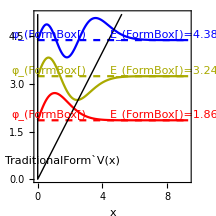

```mathematica
nmax=3;     (* number of Airy functions to plot *)
xmax=9.3; (* maximum position to plot *)
ymax=5.2;
ϵn[n_]:=-2.0^(-1/3)AiryAiZero[n];
φnx[n_,x_]:=2.0^(1/6)AiryAi[2.0^(1/3)x+AiryAiZero[n]]/AiryAiPrime[AiryAiZero[n]]
colors=resistorColorList⟦{3,5,7,9}⟧;
gr=Show[
Plot[Table[ ϵn[n]+φnx[n,x],{n,1,nmax}]//Evaluate,{x,0,xmax},PlotStyle->({#}&/@colors)],
Plot[Table[ ϵn[n],{n,1,nmax}]//Evaluate,{x,0,xmax},PlotStyle->({Dashed,#}&/@colors)],
ImageSize->{216,216},AspectRatio->Full,
AxesOrigin->0,FrameLabel->{"x",""},
PlotRange->{{-0.05,xmax},{0,ymax}},PlotRangePadding->0,PlotRangeClipping->False,
Epilog->{Thick,Line@{{0,ymax},{0,0},{ymax/1.0,ymax}},
Table[{colors⟦n⟧,
Text[StringForm["E_(``)=``",n,ϵn[n]//N//NumberForm[#,3]&],{7.8,ϵn[n]+If[n==5,.1,0]},{0,-1.2}],
Text[StringForm["φ_(``)",n],{.7,ϵn[n]},{0,-1.2}]
},{n,nmax}],
Text["TraditionalForm`V(x)",{1.5,.6}]}
]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/TEX/Bouncer1Eigen.pdf",gr];
```

The figure above shows the potential V(x)=mgx+∞ Θ(-x), eigenenergies E_n, and eigenfunctions φ_n(x).  The plot uses units where m=g=ℏ=1.  The units of length, energy, and wavefunction are x_0=(ℏ^2/(g m^2))^(1/3),  E_0=(ℏ^2 g^2 m)^(1/3),  and φ_0=((g m^2)/ℏ^2)^(1/6).

### Section.Subsection Convergence plots: K(x_f,x_i,T,N_trunc) versus N_trunc

Plot the partial sums versus number of terms for various combinations of x_i,x_f, and t:

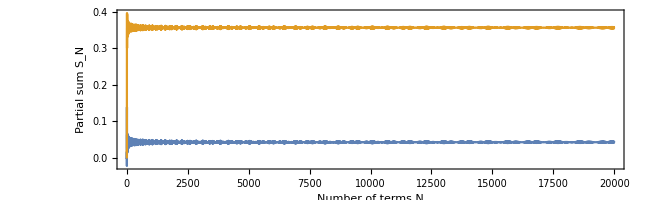

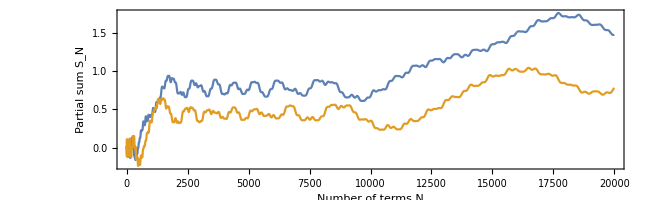

```mathematica
plotConvergence[xi_,xf_,t_]:=Module[{},
termsList=Table[2^(1/3)(AiryAi[2^(1/3)xf+AiryAiZero[n]]AiryAi[2^(1/3)xi+AiryAiZero[n]]Exp[I*AiryAiZero[n]*t/2^(1/3)])/AiryAiPrime[AiryAiZero[n]]^2,{n,1,20000}];
sumsList=Accumulate@termsList;
ListLinePlot[{Re@sumsList,Im@sumsList},ImageSize->{650,200},AspectRatio->Full,Frame->True,FrameLabel->{"Number of terms N","Partial sum S_N"}]
];
plotConvergence[3.,7.,5.]
plotConvergence[3.,7.,0.2]
```

Empirically, the partial sums seem to converge.  For t≫1, convergence is fast, and the eigenfunction expansion is a reasonable way to calculate the propagator.  For small values of t, the terms (and partial sums) are highly self-correlated, and convergence is slow.  In the latter regime, we hypothesize that the path integral method is an alternative method that may give the answer much more efficiently – in fact, one may not even need to perform an infinite sum.

### Section.Subsection Convergence plots: K(x_f,x_i,T,N_trunc) versus x_f for various N_trunc

Now let us study the convergence of the eigenexpansion as a function of x_f.  Airy functions and Airy zeroes are expensive to evaluate in Mathematica, so we optimize the calculation by precalculating ζ_n and C_n=1/[Ai'(ζ_n)]^2 for n=1,2,3,…,N for some N=500, and reusing these values for various values of x_f:

```mathematica
xmax=20.;(* maximum value of Subscript[x, f] at which to calculate and plot K *)
jmax=100;  (* number of Subscript[x, f] points to sample *)
plotConvergence[xi_,t_,nmax_]:=Module[{},
nList=Reverse@Range[nmax,1,-Floor[nmax/20]];
Print[StringForm["N_terms=``",nList]];
(*-------- USER-DEFINED PARAMETERS ABOVE --------*)
ζn=Table[AiryAiZero[n]//N,{n,nmax}];
Cn=Table[2^(1/3)/AiryAiPrime[AiryAiZero[n]]^2//N,{n,nmax}];
xj=Range[0.01,jmax]/jmax*xmax//N;
Ajn=Table[Cn⟦n⟧AiryAi[2^(1/3)xj⟦j⟧+ζn⟦n⟧]AiryAi[2^(1/3)xi+ζn⟦n⟧]Exp[I*ζn⟦n⟧*t/2^(1/3)],{j,jmax},{n,nmax}];(* terms *)
Kjn=Accumulate/@Ajn;  (* partial sums *)
Show[
Table[    ListLinePlot[{xj,Abs@Kjn⟦All,n⟧}ᵀ,PlotStyle->{{AbsoluteThickness@1,GrayLevel[((nmax-n)/nmax)^(.4)]}}],{n,nList}],
ListLinePlot[{{xj,Re@Kjn⟦All,-1⟧}ᵀ,{xj,Im@Kjn⟦All,-1⟧}ᵀ},PlotStyle->{{AbsoluteThickness@1,Blue},{AbsoluteThickness@1,Orange}}],
PlotRange->All,ImageSize->{650,200},AspectRatio->Full,AxesLabel->{"x_f","K"}]
];
```

N_terms={5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

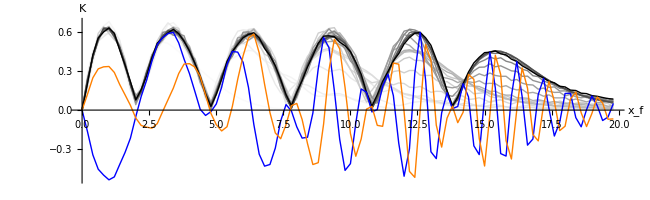

```mathematica
plotConvergence[2.0,2.0,100]
```

The plot above shows K(x_f,x_i=2,t=2) calculated according to the eigenfunction expansion truncated at N terms.
The black curves show |K| for N=5,10,15,…,100.  Darker colors indicate larger N.  Convergence has almost been achieved for N=100.  
The blue and orange curves show Re K and Im K respectively.  We work in a system of units such that g=m=ℏ=1.

N_terms={500,1000,1500,2000,2500,3000,3500,4000,4500,5000,5500,6000,6500,7000,7500,8000,8500,9000,9500,10000}

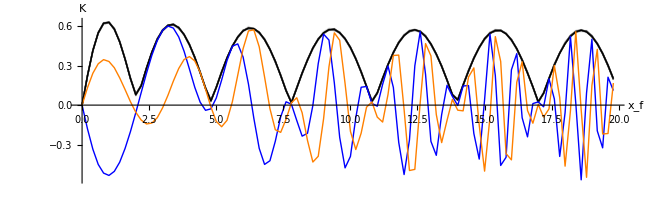

```mathematica
plotConvergence[2.0,2.0,10000]
```

The plot above is for the same parameters, K(x_f,x_i=2,t=2), but for N=500,100,1500,…,10000.  All 20 curves overlap, and only one curve is visible!  Thus, I have extreme confidence in the results above.  Note that |K| is markedly non-sinusoidal at small x_f.

N_terms={500,1000,1500,2000,2500,3000,3500,4000,4500,5000,5500,6000,6500,7000,7500,8000,8500,9000,9500,10000}

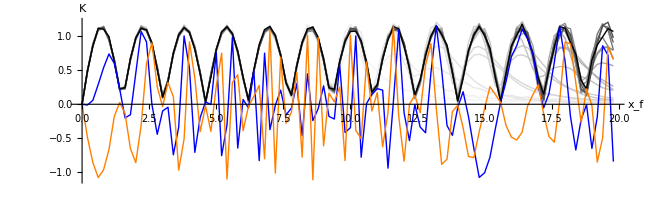

```mathematica
plotConvergence[1.0,0.5,10000]
```

In the plot above, convergence has been achieved, although the results are a bit shaky close to x_f=20.

N_terms={50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950,1000}

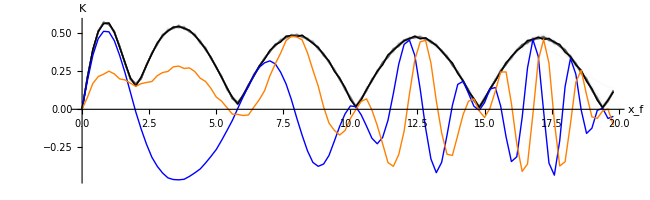

```mathematica
plotConvergence[2,3.0,1000]
```

The plot above shows K(x_f,x_i=0.3,t=6.0).  In this regime, if x_f<6, there are so many different classical paths contributing to the propagator that the behavior of K is quite complicated.

Ultimately, this section shows that the EE method does converge towards a well-defined limit, provided that enough terms are used.  The propagator for the quantum bouncer is evaluatable and plottable, unlike the particle-in-a-box or particle-on-a-ring.

### Section.Subsection Vectorized calculations (I)

Note that	K(x_f,x_i,t)=1/x_0∑_(n=1)^∞ 1/[Ai'(ζ_n)]^2 Ai(x_f/x_0+ζ_n)Ai(x_i/x_0+ζ_n) exp (i ζ_n t)/t_0	where x_0=(ℏ^2/(2g m^2))^(1/3) and  t_0=((2ℏ)/(g^2 m))^(1/3).  
We can calculate {K} for a given t efficiently as follows:
– Define a set of values x_j
– Precalculate ζ_n and c_n=exp (i ζ_n t)/t_0 for n=1,2,3,…,N
– Precalculate A_jn=(Ai(x_j/x_0+ζ_n))/(Ai'(ζ_n)) for j=1,2,3,…,J and n=1,2,3,…,N	
– Compute K(x_i,x_j,t)=1/x_0∑_(n=1)^N A_in A_jn c_n using efficient vectorized operations: K=A·(c*Aᵀ)

```mathematica
g=m=ℏ=1.0;x0=(ℏ^2/(2g m^2))^(1/3);t0=((2ℏ)/(g^2 m))^(1/3);
t=2.;
nn=Range[10000];
ζn=AiryAiZero[nn]//N;
cn=Exp[I ζn t/t0];
xj=Range[.1,10,.1];
Ajn=Table[AiryAi[xj⟦j⟧/x0+ζn]/AiryAiPrime[ζn],{j,Length@xj}];
Kij=Ajn.(cn*Ajnᵀ);
Ajn//Dimensions
Kij//Dimensions
```

{100,10000}

{100,100}

```mathematica
ListContourPlot[Re@Kij,DataRange->{{Min@xj,Max@xj},{Min@xj,Max@xj}},PlotLabel->"TraditionalForm`Re",FrameLabel->{"x_i","x_f"},PlotRangePadding->0]
```

### Section.Subsection Vectorized calculations (II)

The truncated diagonal propagator is
	K_N(x,x,t)=1/x_0∑_(n=1)^N 1/[Ai'(ζ_n)]^2 Ai(x/x_0+ζ_n)Ai(x/x_0+ζ_n) exp (i ζ_n t)/t_0		where x_0=(ℏ^2/(2g m^2))^(1/3)and t_0=((2ℏ)/(g^2 m))^(1/3).
Choose grid points x_j (j=1,2,3,…,J) and t_k (k=1,2,3,…,K).  Then
	K_N(x_(j,)x_j,t_k)=1/x_0∑_(n=1)^N 1/[Ai'(ζ_n)]^2 Ai(X_j+ζ_n)Ai(X_j+ζ_n) exp (i ζ_n t_k)/t_0	where X_j=x_j/x_0
			    =1/x_0∑_(n=1)^N A_n B_jn C_nk		where A_n=1/[Ai'(ζ_n)]^2, B_jn=(Ai(X_j+ζ_n))^2, C_nk=exp (i ζ_n t_k)/t_0
			    =1/x_0∑_(n=1)^N B_jn A_n C_nk
∴	{K_jk}=1/x_0{B_jn}·({A_n}*{C_nk}).
Calculate K_20000 and use K_20000-K_10000 as the error estimate:

```mathematica
g=m=ℏ=1.0;x0=(ℏ^2/(2g m^2))^(1/3);t0=((2ℏ)/(g^2 m))^(1/3);
nmax=10000;
tPoints=40;
xPoints=100;
tk=Rescale[Range@tPoints,{0,tPoints},{0,5}]//N;
xj=Rescale[Range@xPoints,{0,xPoints},{0,10}]//N;
(*-------- CALCULATE SUM UP TO <nmax> TERMS --------*)
nn=Range[1,nmax];
ζn=AiryAiZero[nn]//N;
An=AiryAiPrime[ζn]^-2;
Print@Flatten@AbsoluteTiming@Timing[
Cnk=Outer[Function[{ζ,t},Exp[I ζ t]],ζn,tk/t0];];
Print@Flatten@AbsoluteTiming@Timing[
Bjn=Outer[Function[{X,ζ},AiryAi[X+ζ]],xj/x0,ζn]^2;];
Kjk=Bjn.(An*Cnk)/x0;
(*-------- CALCULATE SUM UP TO <2*nmax> TERMS --------*)
nn=Range[nmax+1,2nmax];
ζn=AiryAiZero[nn]//N;
An=AiryAiPrime[ζn]^-2;
Print@Most@Flatten@AbsoluteTiming@Timing[
Cnk=Outer[Function[{ζ,t},Exp[I ζ t]],ζn,tk/t0];];
Print@Most@Flatten@AbsoluteTiming@Timing[
Bjn=Outer[Function[{X,ζ},AiryAi[X+ζ]],xj/x0,ζn]^2;];
KjkErr=Bjn.(An*Cnk)/x0;
(*-------- COMBINE --------*)
Kjk+=KjkErr;
```

{0.802053,0.940073,Null}

{4.62579,4.64222,Null}

{0.696309,0.888924}

{4.65379,4.7053}

```mathematica
(*Bjn//Dimensions*)
Kjk//Dimensions
KjkErr//Dimensions
```

{100,40}

{100,40}

```mathematica
Row@{
ListPlot3D[Re@Kjk,DataRange->{{Min@tk,Max@tk},{Min@xj,Max@xj}},AxesLabel->{"t","x","Re K"},PlotRange->{All,All,{-2,2}},ImageSize->325],
ListPlot3D[Re@KjkErr,DataRange->{{Min@tk,Max@tk},{Min@xj,Max@xj}},AxesLabel->{"t","x","Re K_err"},PlotRange->{All,All,{-2,2}},ImageSize->325]
}
```

-Graphics3D--Graphics3D-

```mathematica
(*ListContourPlot[Re@Kjk,DataRange->{{Min@tk,Max@tk},{Min@xj,Max@xj}},FrameLabel->{"t","x"},PlotRangePadding->0]*)
```

```mathematica
(*ListDensityPlot[Re@Kjk,DataRange->{{Min@tk,Max@tk},{Min@xj,Max@xj}},FrameLabel->{"t","x"},InterpolationOrder->0]*)
```

### Section.Subsection Vectorized calculations (III)

Consider fixed x_i and variable x_f and T:
	K_N(x_j,x_i,t_k)=1/x_0∑_(n=1)^∞ 1/[Ai'(ζ_n)]^2 Ai(x_j/x_0+ζ_n)Ai(x_i/x_0+ζ_n) exp (i ζ_n t_k)/t_0	 where x_0=(ℏ^2/(2g m^2))^(1/3)and t_0=((2ℏ)/(g^2 m))^(1/3)
			     =1/x_0∑_(n=1)^N A_n B_jn B_in C_nk		where A_n=1/[Ai'(ζ_n)]^2, B_jn=Ai(x_j/x_0+ζ_n), C_nk=exp (i ζ_n t_k)/t_0
			     =1/x_0∑_(n=1)^N B_jn(A_n b_n C_nk)		where b_n≡B_in≡Ai(x_i/x_0+ζ_n) for a fixed i
∴	{K_jk}=1/x_0{B_jn}·({A_n}*{b_n}*{C_nk})	where * means elementwise multiplicatoin.

```mathematica
(*-------- Calculate propagator using eigenexpansion for xf∈xfList and T∈Tlist --------*)
calcKEE[xfList_,xiList_,TList_,nmax_]:=Module[{x0,t0,Xj,Tk,nn,ζn,An,bn,KEEjk},
Print["Parameters are {M,g,ℏ} = ",{M,g,ℏ}];
If[Head@xfList===List&&Head@xiList=!=List&&Head@TList===List,
Print["Calculating K_EE(x_f,x_i,T) for many x_f, one x_i, and many T"],
Print["Error: I don't know what to do!"];Abort[];
];

(*-------- PREPARE VARIABLES --------*)
x0=(ℏ^2/(2g M^2))^(1/3);t0=((2ℏ)/(g^2 M))^(1/3);Xj=xfList/x0;Tk=TList/t0;
(*-------- CALCULATE SUM UP TO <nmax> TERMS --------*)
nn=Range[1,nmax];
ζn=AiryAiZero[nn]//N;
An=AiryAiPrime[ζn]^-2;
Print["Evaluating Exp"];timeIt[    Cnk=Outer[Exp[I*#1*#2]&,ζn,Tk];    ];
Print["Evaluating Airy"];timeIt[    Bjn=Outer[AiryAi[#1+#2]&,Xj,ζn];    ];
Print["Doing BLAS"];
bn=AiryAi[xi/x0+ζn];
KEEjk=Bjn.(An*bn*Cnk)/x0;
Print["Returning array of size ",Dimensions@KEEjk];
Return[KEEjk]
];
```

```mathematica
M=ℏ=1;g=1;nmax=10000;
xi=1;
xfList=Range[0.0625,20.0,0.0625];xPoints=Length@xfList;    (* 80 *)
TList={.25,.5,1,2,3};tPoints=Length@TList;
KEE˘xf˘T=calcKEE[xfList,xi,TList,nmax];
```

Parameters are {M,g,ℏ} = {1,1,1}

Calculating K_EE(x_f,x_i,T) for many x_f, one x_i, and many T

$Aborted

```mathematica
M=ℏ=1;g=1;nmax=10000;
xi=1;
xfList=Range[0.0625,20.0,0.0625];xPoints=Length@xfList;    (* 80 *)
TList={.25,1,4,6};tPoints=Length@TList;
KEE˘xf˘T=calcKEE[xfList,xi,TList,nmax];
```

Parameters are {M,g,ℏ} = {1,1,1}

Calculating K_EE(x_f,x_i,T) for many x_f, one x_i, and many T

Evaluating Exp

Absolute time = 0.115    CPU time = 0.227

Evaluating Airy

Absolute time = 12.5    CPU time = 12.6

Doing BLAS

Returning array of size {320,4}

```mathematica
(*-------- SAVE IN DATA FILE --------*)
data={};
Do[
Kval=KEE˘xf˘T⟦j,k⟧;
AppendTo[data,{xfList⟦j⟧,xi,TList⟦k⟧,Re[Kval],Im[Kval]}];
,{j,xPoints},{k,tPoints}];
Export[NotebookDirectory[]<>"/KEE.dat",data,"Table","FieldSeparators"-> "\t", Alignment-> Left,
TableHeadings->{"xf","xi","T","Re K","Im K"}];
```

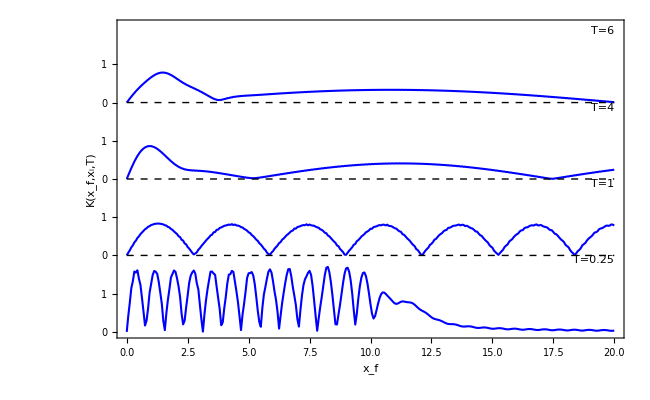

```mathematica
(*-------- PLOT --------*)
offsets=Range@tPoints*2-2;
Show[
ListLinePlot[
Table[{{0,offsets⟦k⟧}}~Join~({xfList,offsets⟦k⟧+Abs@KEE˘xf˘T⟦All,k⟧}ᵀ),{k,tPoints}]//Evaluate,
PlotStyle->{{AbsoluteThickness@1.5,Blue}}
],
PlotLegends->{"K_EE","K_PI0","K_PI"},PlotRange->{{0,Max@xfList},{0,Last@offsets+2}},PlotRangePadding->0,
Frame->True,FrameLabel->{"x_f","K(x_f,x_i,T)"},RotateLabel->True,
FrameTicks->{{
Do[
Do[Sow@{offsets⟦k⟧+y,y,{.012,0}},{y,{0,.5,1,1.5}}];
Do[Sow@{offsets⟦k⟧+y,Null,{.006,0}},{y,0,1.9,.1}];
,{k,tPoints}]//Reap//Last//Last,
Automatic},
{Automatic,Automatic}},
ImageSize->{650,400},AspectRatio->Full,ImagePadding->{{Automatic,Automatic},{Automatic,2}},
PlotRangeClipping->False,
Epilog->{
Table[Text[StringForm["T=``",TList⟦k⟧]//Framed[#,Background->GrayLevel[.9]]&,{20,offsets⟦k⟧+2},{+1,+1}],{k,1,tPoints}],
Dashed,Black,
Table[Line@{{0,offsets⟦k⟧},{Max@xfList,offsets⟦k⟧}},{k,2,tPoints}]
}
]
```

### Section.Subsection Animation: WAVEPACKET EVOLUTION.

Consider wavepacket evolution.  The equations are
	φ_n(x)=(Ai(x/x_0+ζ_n))/(√x_0 Ai'(ζ_n))					Discretize:	U_jn=(Ai(x_j/x_0+ζ_n))/(√x_0 Ai'(ζ_n))
	c_n(0)=∫_0^∞ dx φ_n(x) Ψ(x,0)=δx∑_(n=1)^∞ U_nj Ψ(x,0)
	c_n(t)=∑_(n=1)^∞ (exp (i ζ_n t_k)/t_0)c_n(0)
	Ψ(x,t)=∑_(n=1)^∞ φ_n(x) c_n(t)=∑_(n=1)^∞ U_nj c_n(t)

```mathematica
M=g=ℏ=1;
nmax=10000;
xfList=Range[0.25,50.0,0.25];
(*-------- PREPARE VARIABLES --------*)
xPoints=Length@xfList;    (* 80 *)
x0=(ℏ^2/(2g M^2))^(1/3);t0=((2ℏ)/(g^2 M))^(1/3);Xj=xfList/x0;
(*-------- CALCULATE SUM UP TO <nmax> TERMS --------*)
ζn=AiryAiZero[Range[1,nmax]]//N;
Gn=1/(√x0 AiryAiPrime[ζn]);  (* normalization factor *)
timeIt[    Ujn=Outer[AiryAi[#1+#2]&,Xj,ζn];    ];
Ujn=Gn#&/@Ujn;
```

Absolute time = 7.95    CPU time = 8.12

```mathematica
(*-------- IF INITIAL IS DELTA FUNCTION --------*)
xi=20;
cn0=AiryAiPrime[ζn]^-1*AiryAi[xi/x0+ζn];

(*-------- IF INITIAL IS GWP --------*)
(*{xCen,xWid,kCen}={20,1,2};
cn0=Table[1/(√(√π xWid))Exp[-0.5((x-xCen)/xWid)^2]Exp[+I*kCen*(x-xCen)],{x,xfList}].Ujn*(xfList⟦2⟧-xfList⟦1⟧);*)
```

```mathematica
Manipulate[
cn=cn0*Exp[I*ζn*(t/t0)];(**Exp[.005*ζn];*)  (* convergence factors suppress spurious ghosts at short times? *)
Kj=Ujn.cn;
ListLinePlot[{Abs@Kj(*,Re@Kj,Im@Kj*)},PlotRange->{-.5,1},ImageSize->{1000,300},AspectRatio->Full,
DataRange->{Min@xfList,Max@xfList}]
,{t,0.01,100,Appearance->"Open",AnimationRate->1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Thread::tdlen: Objects of unequal length in {7.6546×10^-11,-1.48685×10^-8,7.86787×10^-7,-0.0000194828,0.000278577,-0.00255545,0.0159177,-0.0691904,0.210432,-0.434848,«9990»} {ⅇ^((0.-1.65 ⅈ) ζn),ⅇ^((0.-1.69231 ⅈ) ζn),ⅇ^((0.-1.73684 ⅈ) ζn),ⅇ^((0.-1.78378 ⅈ) ζn),ⅇ^((0.-1.83333 ⅈ) ζn),ⅇ^((«1») ζn),ⅇ^((0.-1.94118 ⅈ) ζn),ⅇ^((0.-2. ⅈ) ζn),ⅇ^((0.-2.0625 ⅈ) ζn),ⅇ^((0.-2.12903 ⅈ) ζn),«71»} cannot be combined.

Thread::tdlen: Objects of unequal length in {2.718281828459045^((0.-1.65 ⅈ) ζn),2.718281828459045^((0.-1.69231 ⅈ) ζn),2.718281828459045^((0.-1.73684 ⅈ) ζn),2.718281828459045^((0.-1.78378 ⅈ) ζn),(«44»)^((«1») ζn),(«44»)^((0.-«1») ζn),(«44»)^((0.-«18» ⅈ) ζn),2.718281828459045^((0.-2. ⅈ) ζn),2.718281828459045^((0.-2.0625 ⅈ) ζn),2.718281828459045^((0.-2.12903 ⅈ) ζn),«71»} {«22»,«9»,«9990»} cannot be combined.

Thread::tdlen: Objects of unequal length in {2.71828^((0.-1.65 ⅈ) ζn),2.71828^((0.-1.69231 ⅈ) ζn),2.71828^((0.-1.73684 ⅈ) ζn),2.71828^((0.-1.78378 ⅈ) ζn),2.71828^((0.-1.83333 ⅈ) ζn),2.71828^((0.-1.88571 ⅈ) ζn),2.71828^((0.-1.94118 ⅈ) ζn),2.71828^((0.-2. ⅈ) ζn),2.71828^((0.-2.0625 ⅈ) ζn),2.71828^((0.-2.12903 ⅈ) ζn),«71»} {7.6546×10^-11,-1.48685×10^-8,«7»,-0.434848,«9990»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

TO DO: 
- beware of ghosts
- is propagator really that bad?  well yes it is, because discontinuous.  maybe need to try really, really big x and T?   x=20 and T=50?

### Section.Subsection Precalculate normalized eigenfunctions

```mathematica
(*-------- USER-DEFINED STUFF --------*)
nmax=10000;   (* number of Airy functions to use *)
xfList=Range[0,15.0,0.0625]; (* position grid *)

(*-------- PREPARE VARIABLES --------*)
xStep=xfList⟦2⟧-xfList⟦1⟧;
M=g=ℏ=1;xUNIT=(ℏ^2/(2g M^2))^(1/3);tUNIT=((2ℏ)/(g^2 M))^(1/3);  (* we will always use this choice of M, g, and ℏ *)
xPoints=Length@xfList;    (* 80 *)
(*-------- PRECALCULATE EASY THINGS (FAST) --------*)
ζn=AiryAiZero[Range[1,nmax]]//N;    (* Airy zeroes *)
Gn=1/(√xUNIT AiryAiPrime[ζn]);  (* normalization factor *)
(*-------- PRECALCULATE NORMALIZED EIGENFUNCTIONS AS MATRIX (SLOW STEP) --------*)
timeIt[    φnj=Gn*Outer[AiryAi[#1+#2]&,ζn,xfList/xUNIT];    ];
```

Absolute time = 11.4    CPU time = 11.2

### Section.Subsection Complex plot of propagator

```mathematica
(*-------- SET UP TIME EVOLUTION MATRIX --------*)
(*TList=Range[0,50,.05];tPoints=Length@TList;*)
TList=Range[0.03125,25,.03125];tPoints=Length@TList;
timeIt[
Unk=Outer[Function[{ζ,T},Exp[I ζ T]],ζn,TList/tUNIT];
];
```

Absolute time = 16.3    CPU time = 14.9

```mathematica
(*-------- SET UP DELTA FUNCTION --------*)
xi=10;
cn0=AiryAiPrime[ζn]^-1*AiryAi[xi/xUNIT+ζn];
(*-------- TIME-EVOLVE AMPLITUDE COEFFICIENTS --------*)
(*cnk=(cn0*Exp[.005*ζn])*Unk;  (* convergence factors suppress spurious ghosts at short times? *)*)
cnk=cn0*Unk;  (* without convergence factors, stilll not correct at short times *)
(*-------- TRANSFORM TO REAL SPACE --------*)
ψkj=cnkᵀ.φnj;
```

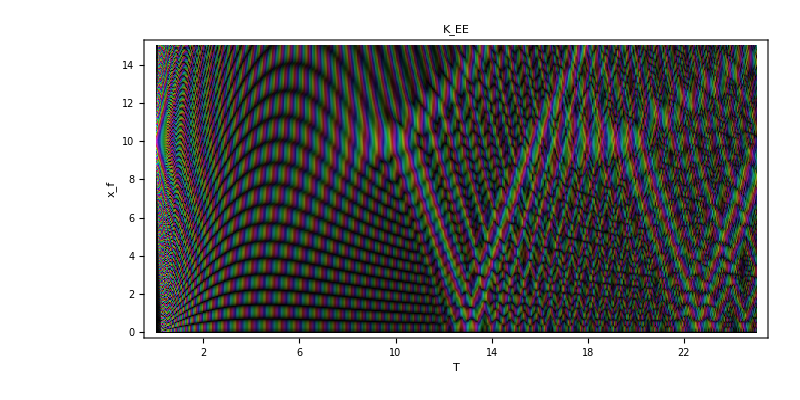

```mathematica
gr=myComplexPlot[TList,xfList,2*ψkj,FrameLabel->Reverse@{"T","x_f"},PlotLabel->"K_EE",ImageSize->{800,400},ImageSize->{648,216}]
```

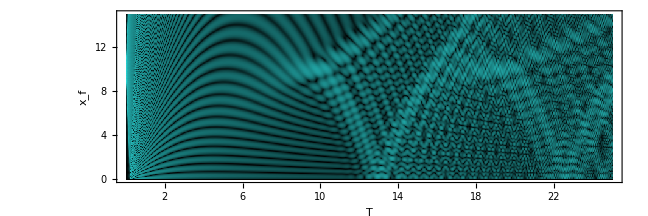

```mathematica
gr2=myRealPlot[TList,xfList,-Abs@ψkj*2.0,FrameLabel->Reverse@{"T","x_f"}]
```

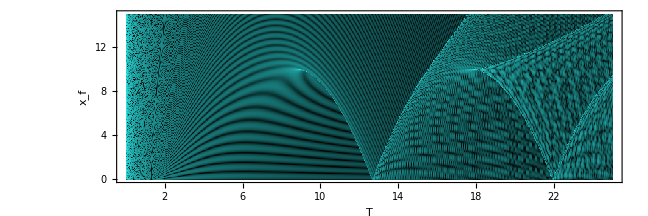

```mathematica
gr2=myRealPlot[TList,xfList,-Abs@data*2.0,FrameLabel->Reverse@{"T","x_f"}]
```

```mathematica
(*Export[ParentDirectory@NotebookDirectory[]<>"/TEX/ColormapKEExi10.png",gr,ImageResolution->200];*)
```

## Section One-Sided Bouncer: FPI

### Section.Subsection Schematic of multi-bounce path with dimension lines

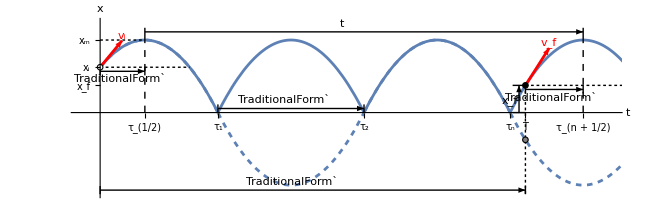

```mathematica
g=1;xm=8;xi=5;xf=3;n=3;
vm=√(2g xm);vi=√(2g(xm-xi));vf=√(2g(xm-xf));tb=(2vm)/g;τi=vi/g;τf=vf/g;
t0=vi/g;(* zeroth zenith *)
tn=t0+n*tb;(* last zenith *)
T=τi+n*tb-τf;
xt[t_]:=xm-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2;
xtSym[t_]:=(xm-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2)(-1)^Floor[(t-t0)/tb+1/2];
gr=Show[
Plot[xt[t],{t,0,tn+τf},PlotStyle->{{AbsoluteThickness@2,ColorData[97]@1}}],
Plot[xtSym[t],{t,0,tn+τf},PlotStyle->{{AbsoluteThickness@2,AbsoluteDashing@{4,4},CapForm@"Butt",ColorData[97]@1}}],
Frame->False,AxesLabel->{"t","x"},Axes->True,AxesOrigin->{0,0},
ImageSize->{648,216},AspectRatio->Full,PlotRange->{{-1,(n+.5)tb},{-xm-1,xm+2}},PlotRangePadding->0,AxesOrigin->{0,0},ImagePadding->{{All,16},{All,16}},PlotRangeClipping->False,
Ticks->{{{t0,"τ_(1/2)"},{t0+tb/2,"τ_1"},{t0+tb/2+tb,"τ_2"},{t0+tb/2+(n-1) tb,"τ_n"},{tn,"τ_(n + 1/2)"},{T,"T"}},{{xi,"x_i"},{xf,"x_f"},{xm,"x_m"}}},
Epilog->{
c=.45;d=.35;
dimLine[{t0,xm},{t0+n tb,xm},"t",3c,2c,4c],
dimLine[{t0+0.5tb,0},{t0+1.5tb,0},"TraditionalForm`",2c,c,3c],
dimLine[{0,xi},{τi,xi},"TraditionalForm`",-2c,-c,-3c],
dimLine[{t0+n tb-τf,xf},{t0+n tb,xf},"TraditionalForm`",-2c,-c,-3c],
dimLine[{0,-9},{T,-9},"TraditionalForm`                                                                  ",2c,c,3c],
dimLine[{T,0},{T,xf},"x_f",2d,d,2.5d],
Dashed,Line@{{{t0,0},{t0,xm}},{{t0+n tb,0},{t0+n tb,xm}}},
Black,AbsoluteDashing@{2,2},
Line@{{0,xm},{t0,xm}},Line@{{0,xi},{2t0,xi}},Line@{{T,xf},{T+2τf,xf}},
Line@{{T,xf},{T,-9}},
Red,Dashing@{},Arrowheads@.025,AbsoluteThickness@2,
Arrow@{{0,xi},{0,xi}+1.2{1,vi}},Text["v_i",{0,xi}+1.2{1,vi},{0,-1}],
Arrow@{{tn-τf,xf},{tn-τf,xf}+1.3{1,vf}},Text["v_f",{tn-τf,xf}+1.3{1,vf},{0,-1}],
(*-------- START AND END POINTS --------*)
Inset[Graphics[{FaceForm[White],EdgeForm@{Thick,Black},Disk[]}],{0,xi},{0,0},Scaled@.05],
Inset[Graphics[{FaceForm[Black],EdgeForm[Black],Disk[]}],{T,xf},{0,0},Scaled@.05],
Inset[Graphics[{FaceForm[Gray],EdgeForm@{Black},Disk[]}],{T,-xf},{0,0},Scaled@.05]
}
]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/TEX/Bouncer1Schematic.pdf",gr];
```

### Section.Subsection Relation between time of flight T and max height x_m

A particularly elegant analysis of this situation is as follows.  Let the total energy of the particle is E.  Then the maximum height that can be reached is x_m=E/(Mg).  The path of the particle can be expanded about the time of maximum height as x(t)=x_m-1/2(g(t-t_m))^2.  The duration of a complete parabolic path is τ=√(8x_m/g).  Let t_0 be the time of the 0th maximum.  If the particle bounces n times (where n is any integer or zero), then the nth maximum occurs at time t_0+nτ.  (This is illustrated in the figure below for n=2.)  If the initial position of the particle is specified to be x_i, then the size of the time interval between the maximum and the initial position is τ_i=√(2(x_m-x_i)/g), as shown in the figure.  So the initial time is t_i=t_0-σ_i τ_i where σ_i=±1.  Similarly, if the final position is x_f, then τ_f=√(2(x_m-x_f)/g), and t_f=t_0+nτ+σ_f τ_f where σ_f=±1.  The duration of the trajectory from (t_i,x_i) to (t_f,x_f) is then 
	T=t_f-t_i=[nτ+σ_f √(2/g(x_m-x_f))]-[-σ_i √(2/g(x_m-x_i))]
∴	T=√(2/g)(2n √x_m+σ_i √(x_m-x_i)+σ_f √(x_m-x_f)) 
where {σ_i,σ_f}⊆{-1,+1}.  This equation is symmetric under interchange of x_i and x_f, and it is elegant because it can be written entirely in terms of the length scales x_i,x_f,x_m, and x_T=√(gT^2/2).

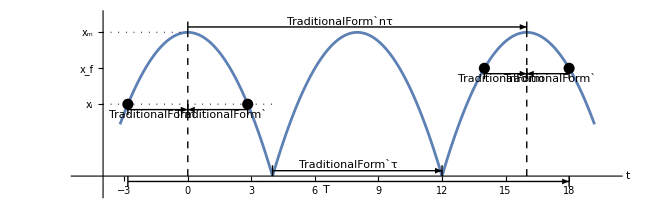

We can invert the equation for T(x_m) to obtain x_m(T).  Nondimensionalization (by setting x_m=(g T^2)/2(x̃)_m, x_i=(g T^2)/2 a, x_f=(g T^2)/2 b) leads to an equation with three square roots, of the form 	
	2n √((x̃)_m)±√((x̃)_m-a)±√((x̃)_m-b)=1.  
This formalism is symmetric in x_i and x_f.  However, it leads to a rather complicated quartic equation for (x̃)_m:

(1+4 a+6 a^2+4 a^3+a^4+4 b+4 a b-4 a^2 b-4 a^3 b+6 b^2-4 a b^2+6 a^2 b^2+4 b^3-4 a b^3+b^4)
+(-8-16 a-8 a^2-16 b+16 a b-8 b^2-16 n^2-16 a n^2+16 a^2 n^2+16 a^3 n^2-16 b n^2-160 a b n^2-16 a^2 b n^2+16 b^2 n^2-16 a b^2 n^2+16 b^3 n^2) (x̃)_m
+(16+32 n^2+128 a n^2-32 a^2 n^2+128 b n^2+64 a b n^2-32 b^2 n^2+96 n^4-64 a n^4+96 a^2 n^4-64 b n^4+64 a b n^4+96 b^2 n^4) ((x̃)_m)^2
+(-128 n^2+128 n^4-256 a n^4-256 b n^4-256 n^6+256 a n^6+256 b n^6) ((x̃)_m)^3
+(256 n^4-512 n^6+256 n^8) ((x̃)_m)^4=0.

### Section.Subsection Relation between time of flight T and max velocity v_m

Since the total energy is E=Mg x_m=1/2 M v_m^2, the maximum height is related to the maximum velocity by x_m=1/(2g)v_m^2.  Thus the equation for T(x_m) can be rewritten as an equation for T(v_m),
	T=1/g(2n v_m+σ_i √(v_m^2-2g x_i)+σ_f √(v_m^2-2g x_f)).

Inverting this equation gives v_m(T).  Nondimensionalize by defining (ṽ)_m=v_m/gT, x_i=(g T^2)/2 a, and x_f=(g T^2)/2 b.  Then 
	2n(ṽ)_m±√(((ṽ)_m)^2-a)±√(((ṽ)_m)^2-b)=1.

The solutions of this equation are the real roots of the quartic equation below, which is still symmetric in x_i and x_f:

16(n^4-n^2) ((ṽ)_m)^4
+ 16(n-2 n^3)((ṽ)_m)^3
+ 4(2a n^2+2b n^2+6 n^2-1) ((ṽ)_m)^2
- 8n(a+b+1) (ṽ)_m
+ (a^2-2ab+b^2+2a+2b+1)=0.

For a given parameter set (x_i,x_f,T,n) there are up to four solutions for the maximum velocity v_m.

If we wish to plot the path corresponding to each value of v_m, we must determine whether σ_i=+1 or -1 such that
	2nw+σ_i √(w^2-a)+σ_f √(w^2-b)=1.
Unfortunately there seems to be no simple way to determine which value of w corresponds to which sign!  Thus this method, though elegant, is not so useful.

#### Derivation

Convert 2nw±√(w^2-a)±√(w^2-b)=1 to a quartic polynomial equation in w:
	±√(w^2-a)±√(w^2-b)=1-2nw
∴	(±√(w^2-a)±√(w^2-b))^2=(2nw-1)^2
∴	w^2-a+w^2-b±2 √(w^2-a)√(w^2-b)=4 n^2 w^2-4nw+1
∴	±2 √(w^2-a)√(w^2-b)=4 n^2 w^2-4nw+1+a+b-2 w^2
∴	4(w^2-a)(w^2-b)=[(4 n^2-2)w^2-4nw+(1+a+b)]^2
∴	4(w^4-a w^2-b w^2+ab)=(4 n^2-2)^2 w^4-16 n^2 w^2+(1+a+b)^2+…
∴	(1+2 a+a^2+2 b-2 a b+b^2)+(-8 n-8 a n-8 b n) w+(-4+24 n^2+8 a n^2+8 b n^2) w^2+(16 n-32 n^3) w^3+(-16 n^2+16 n^4) w^4=0.

Note that the same polynomial equation is obtained regardless of the signs in the initial equation.  We may verify that the polynomial is symmetrical under interchange of a and b:

```mathematica
Clear[a,b,n,w];
Solve[4(w^2-a)(w^2-b)-((4 n^2-2)w^2-4n w+(1+a+b))^2==0,w,Quartics->False]⟦1,1,-1,1⟧@w
polyw[a_,b_,n_,w_]=Solve[2n w+√(w^2-a)+√(w^2-b)==1,w,Quartics->False]⟦1,1,-1,1⟧@w
polyw[a_,b_,n_,w_]=Solve[2n w-√(w^2-a)+√(w^2-b)==1,w,Quartics->False]⟦1,1,-1,1⟧@w
polyw[a_,b_,n_,w_]=Solve[2n w-√(w^2-a)-√(w^2-b)==1,w,Quartics->False]⟦1,1,-1,1⟧@w
```

1+2 a+a^2+2 b-2 a b+b^2+(-8 n-8 a n-8 b n) w+(-4+24 n^2+8 a n^2+8 b n^2) w^2+(16 n-32 n^3) w^3+(-16 n^2+16 n^4) w^4

1+2 a+a^2+2 b-2 a b+b^2+(-8 n-8 a n-8 b n) w+(-4+24 n^2+8 a n^2+8 b n^2) w^2+(16 n-32 n^3) w^3+(-16 n^2+16 n^4) w^4

1+2 a+a^2+2 b-2 a b+b^2+(-8 n-8 a n-8 b n) w+(-4+24 n^2+8 a n^2+8 b n^2) w^2+(16 n-32 n^3) w^3+(-16 n^2+16 n^4) w^4

«1 more identical outputs»

```mathematica
polyw[a,b,n,w]-polyw[b,a,n,w]
```

0

#### Illustration (OLD)

```mathematica
Manipulate[
Plot[{
2n √z+√(z-a)+√(z-b)-1,
2n √z+√(z-a)-√(z-b)-1,
2n √z-√(z-a)+√(z-b)-1,
2n √z-√(z-a)-√(z-b)-1,
10polyz[a,b,n,z]
},{z,0,0.08},PlotRange->{{0,All},{-1,1}},PlotLegends->{"++","+-","-+","--"},
PlotStyle->{Red,Orange,Blue,Purple,Dashed}],
{{a,.003},0,.12,Appearance->"Open"},
{{b,.017},0,.12,Appearance->"Open"},
{{n,3},0,6,1,Appearance->"Open"},ControlPlacement->Right
]
```

### Section.Subsection Relation between time of flight T and initial velocity v_i

In this section we present an extremely concise solution of the path enumeration problem for the classical bouncer.

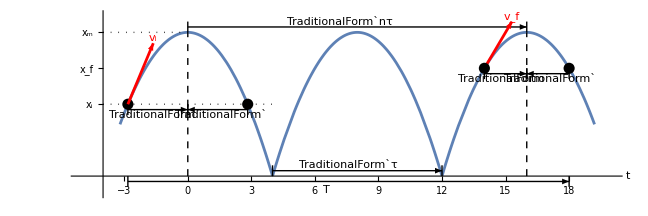

From the diagram above, the time interval between bounces is τ=(2 v_m)/g=2/g √(2g x_i+v_i^2).  The time elapsed from start to end is T=τ_i+nτ-τ_f=v_i/g+n((2 v_m)/g)-v_f/g, so v_f=v_i-gT+2n v_m.  Alternatively, by considering the changes in velocity due to gravity and elastic collisions, we obtain the same result,
	v_f=v_i-gT+2n v_m.
From energy conservation 1/2 M v^2+Mgx=E, or from the free-fall kinematic equations, we obtain
	v_m^2=v_i^2+2g x_i=v_f^2+2g x_f.

Suppose the initial velocity v_i is given.  Eliminate v_f and v_m to get an equation for v_i in terms of x_i,x_f, and T, with no sign ambiguity:
	v_i^2+2g(x_i-x_f)=(2n √(v_i^2+2g x_i)+v_i-gT)^2.
Nondimensionalization:  Let x_i=(g T^2)/2 a, x_f=(g T^2)/2 b, v_i=gTu, v_f=gTv, v_m=gTw, n=k/2.  Then the above equations become
	v=u-1+2nw,
	w^2=u^2+a=v^2+b,
	u^2+a-b=(k √(u^2+a)+u-1)^2.
Quartic equation:  Rationalizing gives
	u^2+a-b=k^2(u^2+a)+(u-1)^2+2k(u-1)√(u^2+a)
∴	2k(u-1)√(u^2+a)=(1-k^2)(u^2+a)-b-(u-1)^2
∴	2k(u-1)√(u^2+a)=u^2-k^2 u^2+a-k^2 a-b-u^2+2u-1
∴	2k(u-1)√(u^2+a)=-k^2 u^2+2u+a-k^2 a-b-1
∴	4(k^2(u-1))^2(u^2+a)=(k^2 u^2-2u+k^2 a+b-a+1)^2
∴	…

Expanding and simplifying, we find that u≡(ṽ)_i satisfies a quartic equation:

16(n^4-n^2) ((ṽ)_i)^4
+16 n^2 ((ṽ)_i)^3
+ [32 n^4 a+8n^2(b-1-3a)+4] ((ṽ)_i)^2
+ 4(4 n^2 a+a-b-1) (ṽ)_i
+ [16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2]=0
where a=(2 x_i)/(g T^2),b=(2 x_f)/(g T^2),(ṽ)_i=v_i/gT.

In this formulation of the problem we look for solutions for v_i.  The equations are asymmetrical in x_i and x_f and somewhat less elegant than the previous formulations.  However, the present formalism has the advantage that it gives the signs of v_i explicitly, so there is no need to “backtrack” to determine σ_i as in the previous formulations.

Once we have found v_i, we can calculate the maximum speed v_m=√(2g x_i+v_i^2), the time between bounces τ=(2 v_m)/g, the maximum height x_m=v_m^2/(2g), and the time of the zeroth maximum t_0=v_i/g.  The time of the kth maximum is t_k=t_0+kτ.  Thus, the number of the maximum closest to time t is k=⌊(t-t_0)/τ+1/2⌋.  It can be shown that the path is

x(t)=x_m-g/2(t-t_0-τ⌊(t-t_0)/τ+1/2⌋)^2.

#### Code

```mathematica
Clear[a,b,n,k,u];
polyu=Solve[u^2+a-b==(k √(u^2+a)+u-1)^2,u,Quartics->False]⟦1,1,2,1⟧@u/.{k->2n}
polyu=Solve[4 k^2(u-1)^2(u^2+a)==(k^2 u^2-2u+k^2 a+b-a+1)^2,u,Quartics->False]⟦1,1,2,1⟧@u/.{k->2n}
```

1-2 a+a^2+2 b-2 a b+b^2-8 a n^2-8 a^2 n^2+8 a b n^2+16 a^2 n^4+(-4+4 a-4 b+16 a n^2) u+(4-8 n^2-24 a n^2+8 b n^2+32 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4

1-2 a+a^2+2 b-2 a b+b^2-8 a n^2-8 a^2 n^2+8 a b n^2+16 a^2 n^4+(-4+4 a-4 b+16 a n^2) u+(4-8 n^2-24 a n^2+8 b n^2+32 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4

```mathematica
(*polyu2=Solve[16(n^4-n^2)u^4+16 n^2 u^3+(32 n^4 a+8 n^2(b-1-3a)+4)u^2+4(4 n^2 a+a-b-1)u+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)==0,u,Quartics->False]⟦1,1,2,1⟧@u
polyu2-polyu//Simplify*)
```

```mathematica
Solve[polyu==0/.n->0,u,Cubics->False,Quartics->False]
Solve[polyu==0/.n->1,u,Cubics->False,Quartics->False]⟦1,1,2,1⟧@u==0
Solve[polyu==0,u,Cubics->False,Quartics->False]⟦1,1,2,1⟧@u==0
```

{{u→1/2 (1-a+b)},{u→1/2 (1-a+b)}}

1+6 a+9 a^2+2 b+6 a b+b^2+(-4+68 a-4 b) u+(-4+8 a+8 b) u^2+16 u^3==0

1-2 a+a^2+2 b-2 a b+b^2+8 a n^2-8 a^2 n^2+8 a b n^2+16 a^2 n^4+(-4+4 a-4 b+64 a n^2) u+(4-8 n^2-24 a n^2+8 b n^2+32 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4==0

#### Alternative derivation

Suppose a particle starts with vertical position x_i and velocity v_i at time t_i=0, suppose a particle bounces n times.  Apply the kinematic equation for displacement in going from t=0 till the first bounce: x(t)=x_i+v_i t-1/2 g t^2 if t=t_1 (time of first bounce).  So
	0=x_i+v_i t_1-1/2 g t_1^2
∴	0=x_i+v_i t_1-1/2 g t_1^2
∴	t_1=(v_i+√(v_i^2+2g x_i))/g.
The positive root above is the physical solution.  Nevertheless we will find it convenient to define the time of the zeroth bounce, extrapolated backwards from the initial conditions, as
	t_0=(v_i-√(v_i^2+2g x_i))/g		(note that t_0<0).

The maximum velocity, which occurs at the moment of impact, can be found from the kinematic velocity equation -v_max=v_i-g t_1=-√(v_i^2+2g x_i).  So
	v_max=√(v_i^2+2g x_i).	
The time interval between the first and second bounces can be found from the kinematic velocity equation -v_b=+v_b-gΔt.  This gives
	Δt=(2 √(v_i^2+2g x_i))/g.	
The time of the nth bounce is
	t_n=t_0+nΔt=(v_i-√(v_i^2+2g x_i))/g+n(2 √(v_i^2+2g x_i))/g=(v_i+(2n-1)√(v_i^2+2g x_i))/g.
For a given time t, the number of bounces that have occurred, n, is given by the largest integer n such that t_n≤t.  In other words, t_0+nΔt≤t.  so
	n=⌊(t-t_0)/Δt⌋.

The kinematic displacement equation then gives the position at time t as
	x(t)=0+v_max(t-t_n)-1/2(g(t-t_n))^2
	      =√(v_i^2+2g x_i)(t-t_n)-1/2(g(t-t_n))^2  where t_n=v_i/g-(√(v_i^2+2g x_i))/g+(2 √(v_i^2+2g x_i))/g⌊(gt-v_i)/(2 √(v_i^2+2g x_i))-1/2⌋.

The solution of the classical bouncer, defined by Newton’s laws with a hard-wall-and-ramp potential as below,
	m x^(..)=-dV/dx where V(x)=Piecewise[{{∞, x<0}, {mgx, x>0}}]		x(0)=x_i		v(0)=u
can be written as
	x(t)=√(v_i^2+2g x_i)(t-(v_i/g-(√(v_i^2+2g x_i))/g+(2 √(v_i^2+2g x_i))/g⌊(gt-v_i)/(2 √(v_i^2+2g x_i))-1/2⌋))-1/2 g(t-(v_i/g-(√(v_i^2+2g x_i))/g+(2 √(v_i^2+2g x_i))/g⌊(gt-v_i)/(2 √(v_i^2+2g x_i))-1/2⌋)^2).

If the number of bounces n is declared in advance, then the position at time T is simply
	x_f=v_max(T-t_n)-1/2(g(T-t_n))^2
	    =v_max(T-(v_i+(2n-1)v_max)/g)-g/2(T-(v_i+(2n-1)v_max)/g)^2						using t_n=(v_i+(2n-1)v_max)/g
	    =-1/(2g)[gT-v_i-(2n+1) √(v_i^2+2g x_i)][gT-v_i-(2n-1) √(v_i^2+2g x_i)]		using v_max=√(v_i^2+2g x_i)
	    =-1/(2g)[(gT-v_i)^2+(4 n^2-1) (v_i^2+2g x_i)-4n(gT-v_i)√(v_i^2+2g x_i)]			expanding.
This gives a formula for the final position as

x_f=1/(2g)[4n(gT-v_i)√(v_i^2+2g x_i)-(gT-v_i)^2-(4 n^2-1) (v_i^2+2g x_i)].

### Section.Subsection Discriminant analysis

The classical bouncer has only two dimensionless parameters, which are the scaled initial and final altitudes a and b.  However, in this study we fix x_i, and let x_f and T vary.  The possible initial velocities v_i=ugT are roots of a quartic polynomial equation involving the initial altitude x_i=ag T^2 and final altitude x_f=bg T^2.  Given T and x_f, we have a=x_i/(g T^2) and b=x_f/(g T^2).  Let D(a,b) be the discriminant of the quartic polynomial.  We wish to plot zero contours of D in (T,x_f) space, that is, the curves where D(x_i/(g T^2),x_f/(g T^2))=0.

If n=0, the quartic equation for (ṽ)_i reduces to a quadratic equation.  The discriminant is
	D_0=0
which indicates a double root.  Indeed, solving the quadratic, we find that there is exactly one solution for the initial velocity, which is
	(ṽ)_i=(1+b-a)/2.

If n=1, the quartic equation for (ṽ)_i reduces to a cubic equation.  The discriminant of this cubic is
	D_1=-65536 (3+3a+b)^2 [8(a+b)^3+15(a+b)^2+6(a+b)-1-108ab].

If n=2,3,4,…, the quartic equation for (ṽ)_i is a general quartic equation.  The discriminant is 
	𝒟_n(a,b)=4096(c^2[b+(a+1)(c-1)])^2×[
1+(2-2c)s+(1-8c+c^2)s^2+(-4+20c+2 c^2)a b
+(-10c+2 c^2)s^3+(40c-2 c^2-2 c^3)a b s
+(-64c+48 c^2-12 c^3+c^4)a^2 b^2+(32c-16 c^2+2 c^3)a b s^2+(-4c+c^2)s^4]
where c=4 n^2 and s=a+b.

For the simple classical bouncer, the initial velocity v_i(x_i,x_f,T,n) is the root of an algebraic equation.
For n=0, v_i is a degenerate root of a quadratic equation, so there is only one solution.
For n=1, v_i is a real root of a cubic polynomial.  There may be 1 or 3 solutions.
For n≥2, v_i is a real root of a quartic polynomial.  There may be 0, 2, or 4 solutions.

Recall that a=x_i/(g T^2) and b=x_f/(g T^2).  We can plot phase diagrams for the classical bouncer by plotting the isosurfaces of D_n(x_i/(g T^2),x_f/(g T^2))=0 in (x_i,x_f,T) space.  We can fix T and plot contours D_n(x_i/(g T^2),x_f/(g T^2))=0 in (x_i,x_f) space.  Alternatively, we can fix x_i and plot contours D_n(x_i/(g T^2),x_f/(g T^2))=0 in (T,x_f) space.  The result can be stated as follows:

#### Code: calculate polynomial and discriminant

```mathematica
Clear[n,a,b,u,polyu];
polyu[n_,a_,b_,u_]=1-2 a+a^2+2 b-2 a b+b^2-8 a n^2-8 a^2 n^2+8 a b n^2+16 a^2 n^4+(-4+4 a-4 b+16 a n^2) u+(4-8 n^2-24 a n^2+8 b n^2+32 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4//
FullSimplify//Expand//Collect[#,u]&;
Print["P_n(a,b,u)=",polyu[n,a,b,u]];
discu[n_,a_,b_]=Discriminant[polyu[n,a,b,u],u]//FullSimplify;
myDiscrim=discu[n,a,b]/.n->(√c)/2//FullSimplify//Factor;
myFactors=List@@myDiscrim//Simplify;Print["𝒟_n(a,b)=",Cross@@myFactors]
```

P_n(a,b,u)=1-2 a+a^2+2 b-2 a b+b^2-8 a n^2-8 a^2 n^2+8 a b n^2+16 a^2 n^4+(-4+4 a-4 b+16 a n^2) u+(4-8 n^2-24 a n^2+8 b n^2+32 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4

𝒟_n(a,b)=4096×c^2×(-1+b+a (-1+c)+c)^2×(a^4 (-4+c) c+(1+b)^2 (1-2 b c+b^2 (-4+c) c)+a^2 (1-2 (4-5 b+12 b^2) c+(1+4 b+22 b^2) c^2-2 b (1+4 b) c^3+b^2 c^4)+2 a^3 c (-5+c+b (8-6 c+c^2))+2 a (1-c+b^2 c (5+2 c-c^2)+b^3 c (8-6 c+c^2)+b (-1+2 c+2 c^2)))

Simplify 3rd factor:

```mathematica
myFactors⟦3⟧-(b+(a+1)(c-1))^2//Simplify
```

0

Simplify 4th factor:

```mathematica
fac=myFactors⟦4⟧//FullSimplify
```

a^4 (-4+c) c+2 a^3 c (-5+b (-4+c) (-2+c)+c)+(1+b)^2 (1+b (-2+b (-4+c)) c)+2 a (1-c+b (-1+2 c (1+c)+b c (5+b (-4+c) (-2+c)-(-2+c) c)))+a^2 (1+c (-8+c+b (10-2 (-2+c) c+b (-4+c) (6+(-4+c) c))))

Try writing in terms of symmetric combinations of a and b:

```mathematica
blah=1+(2-2c)(a+b)+(1-8c+c^2)(a^2+b^2)+(-2+4c+4 c^2)(a b)+(-10c+2 c^2)(a^3+b^3)+(10c+4 c^2-2 c^3)(a^2 b+a b^2)+(-4c+c^2)(a^4+b^4)+(16 c-12 c^2+2 c^3)(a^3 b+a b^3)+(-24 c+22 c^2-8 c^3+c^4)a^2 b^2;
fac-blah//Simplify
blah
```

0

1+(a+b) (2-2 c)+(a^2+b^2) (1-8 c+c^2)+(a^4+b^4) (-4 c+c^2)+(a^3+b^3) (-10 c+2 c^2)+a b (-2+4 c+4 c^2)+(a^2 b+a b^2) (10 c+4 c^2-2 c^3)+(a^3 b+a b^3) (16 c-12 c^2+2 c^3)+a^2 b^2 (-24 c+22 c^2-8 c^3+c^4)

Try writing in terms of s=a+b and d=a-b:

```mathematica
fac/.Solve[{s==(a+b)/2,d==(a-b)/2},{a,b}]//Last//FullSimplify//Expand//Collect[#,{s,d}]&
```

1+(4-20 c-2 c^2) d^2+(-64 c+48 c^2-12 c^3+c^4) d^4+(4-4 c+(-80 c+4 c^2+4 c^3) d^2) s+(-12 c+6 c^2+(-32 c^2+16 c^3-2 c^4) d^2) s^2+(12 c^2-4 c^3) s^3+(-4 c^3+c^4) s^4

Try writing in terms of s=a+b and p=ab:

```mathematica
fac/.Solve[{s==a+b,p==a b},{a,b}]//Last//FullSimplify//Expand//Collect[#,{s,p}]&
%/.{p->a b,s->(a+b)}
```

1+(-4+20 c+2 c^2) p+(-64 c+48 c^2-12 c^3+c^4) p^2+(2-2 c+(40 c-2 c^2-2 c^3) p) s+(1-8 c+c^2+(32 c-16 c^2+2 c^3) p) s^2+(-10 c+2 c^2) s^3+(-4 c+c^2) s^4

1+(a+b)^4 (-4 c+c^2)+(a+b)^3 (-10 c+2 c^2)+a b (-4+20 c+2 c^2)+a^2 b^2 (-64 c+48 c^2-12 c^3+c^4)+(a+b) (2-2 c+a b (40 c-2 c^2-2 c^3))+(a+b)^2 (1-8 c+c^2+a b (32 c-16 c^2+2 c^3))

Verify:

```mathematica
(
1
+(2-2c)(a+b)
+(1-8c+c^2)(a+b)^2+(-4+20c+2 c^2)a b
+(-10c+2 c^2)(a+b)^3+(40c-2 c^2-2 c^3)a b(a+b)
+(-64c+48 c^2-12 c^3+c^4)a^2 b^2+(32c-16 c^2+2 c^3)a b(a+b)^2+(-4c+c^2)(a+b)^4
)-
fac//FullSimplify
```

0

The discriminant is
	𝒟_n(a,b)=4096(c^2[b+(a+1)(c-1)])^2×[
1
+(2-2c)(a+b)
+(1-8c+c^2)(a+b)^2+(-4+20c+2 c^2)a b
+(-10c+2 c^2)(a+b)^3+(40c-2 c^2-2 c^3)a b(a+b)
+(-64c+48 c^2-12 c^3+c^4)a^2 b^2+(32c-16 c^2+2 c^3)a b(a+b)^2+(-4c+c^2)(a+b)^4
]
where c=4 n^2.

```mathematica
(
1
+(2-2c)(a+b)
+(1-8c+c^2)(a+b)^2+(-4+20c+2 c^2)a b
+(-10c+2 c^2)(a+b)^3+(40c-2 c^2-2 c^3)a b(a+b)
+(-64c+48 c^2-12 c^3+c^4)a^2 b^2+(32c-16 c^2+2 c^3)a b(a+b)^2+(-4c+c^2)(a+b)^4
)//HoldForm//TeXForm
```

1+(2-2 c) (a+b)+\left(1-8 c+c^2\right) (a+b)^2+\left(-4+20 c+2 c^2\right) a b+\left(-10 c+2 c^2\right) (a+b)^3+\left(40 c-2 c^2-2 c^3\right) a b (a+b)+\left(-64
   c+48 c^2-12 c^3+c^4\right) a^2 b^2+\left(32 c-16 c^2+2 c^3\right) a b (a+b)^2+\left(-4 c+c^2\right) (a+b)^4

#### Alternative: coefficient arrays

Write in terms of coefficient arrays:

```mathematica
fac=myFactors⟦4⟧/.n->(√c)/2//Expand
MatrixForm@CoefficientList[fac,{a,b}]
MatrixForm/@CoefficientList[fac,{c,a,b}]
```

1+2 a+a^2+2 b-2 a b+b^2-2 a c-8 a^2 c-10 a^3 c-4 a^4 c-2 b c+4 a b c+10 a^2 b c+16 a^3 b c-8 b^2 c+10 a b^2 c-24 a^2 b^2 c-10 b^3 c+16 a b^3 c-4 b^4 c+a^2 c^2+2 a^3 c^2+a^4 c^2+4 a b c^2+4 a^2 b c^2-12 a^3 b c^2+b^2 c^2+4 a b^2 c^2+22 a^2 b^2 c^2+2 b^3 c^2-12 a b^3 c^2+b^4 c^2-2 a^2 b c^3+2 a^3 b c^3-2 a b^2 c^3-8 a^2 b^2 c^3+2 a b^3 c^3+a^2 b^2 c^4

(1 | 2-2 c | 1-8 c+c^2 | -10 c+2 c^2 | -4 c+c^2
2-2 c | -2+4 c+4 c^2 | 10 c+4 c^2-2 c^3 | 16 c-12 c^2+2 c^3 | 0
1-8 c+c^2 | 10 c+4 c^2-2 c^3 | -24 c+22 c^2-8 c^3+c^4 | 0 | 0
-10 c+2 c^2 | 16 c-12 c^2+2 c^3 | 0 | 0 | 0
-4 c+c^2 | 0 | 0 | 0 | 0)

{(1 | 2 | 1 | 0 | 0
2 | -2 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | -2 | -8 | -10 | -4
-2 | 4 | 10 | 16 | 0
-8 | 10 | -24 | 0 | 0
-10 | 16 | 0 | 0 | 0
-4 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 2 | 1
0 | 4 | 4 | -12 | 0
1 | 4 | 22 | 0 | 0
2 | -12 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0
0 | -2 | -8 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)}

#### Code: n=0

```mathematica
polyu[0,a,b,u]
Solve[%==0,u]//Union//Last//Last
```

1-2 a+a^2+2 b-2 a b+b^2+(-4+4 a-4 b) u+4 u^2

u→1/2 (1-a+b)

#### Code: n=1

```mathematica
polyu[1,a,b,u]
discu[1,a,b]//FullSimplify
```

1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) u+(-4+8 a+8 b) u^2+16 u^3

-65536 (3+3 a+b)^2 (8 a^3+(1+b)^2 (-1+8 b)+3 a^2 (5+8 b)+6 a (1+b (-13+4 b)))

```mathematica
asdf=(8 a^3+(1+b)^2 (-1+8 b)+3 a^2 (5+8 b)+6 a (1+b (-13+4 b)))//Expand
asdf-(8(a+b)^3+15(a+b)^2+6(a+b)-1-108a b)//Simplify
```

-1+6 a+15 a^2+8 a^3+6 b-78 a b+24 a^2 b+15 b^2+24 a b^2+8 b^3

0

```mathematica
(*%//TeXForm*)
```

#### Code: n≥2

```mathematica
discu[n,a,b]//FullSimplify
```

65536 n^4 (1+a-b-4 (1+a) n^2)^2 (1+2 a+a^2+2 b-2 a b+b^2-8 (a+2 a^4+a^3 (5-8 b)+b (1+b)^2 (1+2 b)-a b (2+b (5+8 b))+a^2 (4+b (-5+12 b))) n^2+16 (a^4+a^3 (2-12 b)+b^2 (1+b)^2+4 a b (1+b-3 b^2)+a^2 (1+4 b+22 b^2)) n^4+128 a b (a^2+(-1+b) b-a (1+4 b)) n^6+256 a^2 b^2 n^8)

```mathematica
(1+2 a+a^2+2 b-2 a b+b^2-8 (a+2 a^4+a^3 (5-8 b)+b (1+b)^2 (1+2 b)-a b (2+b (5+8 b))+a^2 (4+b (-5+12 b))) n^2+16 (a^4+a^3 (2-12 b)+b^2 (1+b)^2+4 a b (1+b-3 b^2)+a^2 (1+4 b+22 b^2)) n^4+128 a b (a^2+(-1+b) b-a (1+4 b)) n^6+256 a^2 b^2 n^8)/.{a->z a,b->z b}//Collect[#,z]&
%/.z->"1"
```

1+(2 a+2 b-8 a n^2-8 b n^2) z+(a^2-2 a b+b^2-32 a^2 n^2+16 a b n^2-32 b^2 n^2+16 a^2 n^4+64 a b n^4+16 b^2 n^4) z^2+(-40 a^3 n^2+40 a^2 b n^2+40 a b^2 n^2-40 b^3 n^2+32 a^3 n^4+64 a^2 b n^4+64 a b^2 n^4+32 b^3 n^4-128 a^2 b n^6-128 a b^2 n^6) z^3+(-16 a^4 n^2+64 a^3 b n^2-96 a^2 b^2 n^2+64 a b^3 n^2-16 b^4 n^2+16 a^4 n^4-192 a^3 b n^4+352 a^2 b^2 n^4-192 a b^3 n^4+16 b^4 n^4+128 a^3 b n^6-512 a^2 b^2 n^6+128 a b^3 n^6+256 a^2 b^2 n^8) z^4

1+1 (2 a+2 b-8 a n^2-8 b n^2)+1^2 (a^2-2 a b+b^2-32 a^2 n^2+16 a b n^2-32 b^2 n^2+16 a^2 n^4+64 a b n^4+16 b^2 n^4)+1^3 (-40 a^3 n^2+40 a^2 b n^2+40 a b^2 n^2-40 b^3 n^2+32 a^3 n^4+64 a^2 b n^4+64 a b^2 n^4+32 b^3 n^4-128 a^2 b n^6-128 a b^2 n^6)+1^4 (-16 a^4 n^2+64 a^3 b n^2-96 a^2 b^2 n^2+64 a b^3 n^2-16 b^4 n^2+16 a^4 n^4-192 a^3 b n^4+352 a^2 b^2 n^4-192 a b^3 n^4+16 b^4 n^4+128 a^3 b n^6-512 a^2 b^2 n^6+128 a b^3 n^6+256 a^2 b^2 n^8)

```mathematica
Clear[n,xi,xf,g,T];
discu[n,(2xi)/(g T^2),(2xf)/(g T^2)]//Simplify//Factor
Solve[discu[n,(2xi)/gT2,(2xf)/gT2]==0,{gT2},Cubics->False,Quartics->False]⟦-1,1,2⟧
%⟦1⟧@(g T^2)
```

1/(g^6 T^12)65536 n^4 (-g T^2+4 g n^2 T^2+2 xf-2 xi+8 n^2 xi)^2 (g^4 T^8+4 g^3 T^6 xf-16 g^3 n^2 T^6 xf+4 g^2 T^4 xf^2-128 g^2 n^2 T^4 xf^2+64 g^2 n^4 T^4 xf^2-320 g n^2 T^2 xf^3+256 g n^4 T^2 xf^3-256 n^2 xf^4+256 n^4 xf^4+4 g^3 T^6 xi-16 g^3 n^2 T^6 xi-8 g^2 T^4 xf xi+64 g^2 n^2 T^4 xf xi+256 g^2 n^4 T^4 xf xi+320 g n^2 T^2 xf^2 xi+512 g n^4 T^2 xf^2 xi-1024 g n^6 T^2 xf^2 xi+1024 n^2 xf^3 xi-3072 n^4 xf^3 xi+2048 n^6 xf^3 xi+4 g^2 T^4 xi^2-128 g^2 n^2 T^4 xi^2+64 g^2 n^4 T^4 xi^2+320 g n^2 T^2 xf xi^2+512 g n^4 T^2 xf xi^2-1024 g n^6 T^2 xf xi^2-1536 n^2 xf^2 xi^2+5632 n^4 xf^2 xi^2-8192 n^6 xf^2 xi^2+4096 n^8 xf^2 xi^2-320 g n^2 T^2 xi^3+256 g n^4 T^2 xi^3+1024 n^2 xf xi^3-3072 n^4 xf xi^3+2048 n^6 xf xi^3-256 n^2 xi^4+256 n^4 xi^4)

Root[-256 n^2 xf^4+256 n^4 xf^4+1024 n^2 xf^3 xi-3072 n^4 xf^3 xi+2048 n^6 xf^3 xi-1536 n^2 xf^2 xi^2+5632 n^4 xf^2 xi^2-8192 n^6 xf^2 xi^2+4096 n^8 xf^2 xi^2+1024 n^2 xf xi^3-3072 n^4 xf xi^3+2048 n^6 xf xi^3-256 n^2 xi^4+256 n^4 xi^4+(-320 n^2 xf^3+256 n^4 xf^3+320 n^2 xf^2 xi+512 n^4 xf^2 xi-1024 n^6 xf^2 xi+320 n^2 xf xi^2+512 n^4 xf xi^2-1024 n^6 xf xi^2-320 n^2 xi^3+256 n^4 xi^3) #1+(4 xf^2-128 n^2 xf^2+64 n^4 xf^2-8 xf xi+64 n^2 xf xi+256 n^4 xf xi+4 xi^2-128 n^2 xi^2+64 n^4 xi^2) #1^2+(4 xf-16 n^2 xf+4 xi-16 n^2 xi) #1^3+#1^4&,4]

g^4 T^8-256 n^2 xf^4+256 n^4 xf^4+1024 n^2 xf^3 xi-3072 n^4 xf^3 xi+2048 n^6 xf^3 xi-1536 n^2 xf^2 xi^2+5632 n^4 xf^2 xi^2-8192 n^6 xf^2 xi^2+4096 n^8 xf^2 xi^2+1024 n^2 xf xi^3-3072 n^4 xf xi^3+2048 n^6 xf xi^3-256 n^2 xi^4+256 n^4 xi^4+g^3 T^6 (4 xf-16 n^2 xf+4 xi-16 n^2 xi)+g^2 T^4 (4 xf^2-128 n^2 xf^2+64 n^4 xf^2-8 xf xi+64 n^2 xf xi+256 n^4 xf xi+4 xi^2-128 n^2 xi^2+64 n^4 xi^2)+g T^2 (-320 n^2 xf^3+256 n^4 xf^3+320 n^2 xf^2 xi+512 n^4 xf^2 xi-1024 n^6 xf^2 xi+320 n^2 xf xi^2+512 n^4 xf xi^2-1024 n^6 xf xi^2-320 n^2 xi^3+256 n^4 xi^3)

```mathematica
(*%/.{xi->Subscript[x, i],xf->Subscript[x, f]}*)
```

#### Upper bound on number of bounces

In the case of general n, find the points along the a=b line and the b=0 line where D_n=0:

```mathematica
Solve[discu[n,a,0]==0,a,Assumptions->n∈Integers&&n>2]
```

{{a→-1},{a→1/(-4 n+4 n^2)},{a→1/(4 n+4 n^2)}}

```mathematica
Solve[discu[n,a,a]==0,a,Assumptions->n∈Integers&&n>2]
```

{{a→1/(4 n^2)},{a→(1-4 n^2)/(4 n^2)},{a→1/(-4+4 n^2)}}

### Section.Subsection Phase diagram as function of (x_f,T) for fixed x_i

#### Crude method

```mathematica
nPaths[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{uSols,vi,n,nmax,a,b,vm,vf,S,k,u,v,w,dSdxidxf},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
Length@u
];
```

```mathematica
(*-------- USER-DEFINED PARAMETERS --------*)
xi=10;
xfList=Range[0.0625,15.0,8* 0.0625]; (* position grid *)
TList=Range[0.03125,25,8 *.03125];
Monitor[timeIt[   data=Table[nPaths[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]    ],{T,xf}];
```

Absolute time = 4.33    CPU time = 4.29

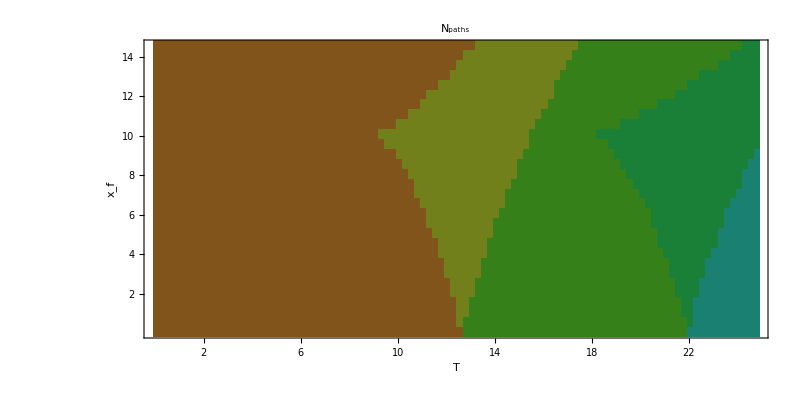

```mathematica
gr=myComplexPlot[TList,xfList,Exp[.3I data],FrameLabel->Reverse@{"T","x_f"},PlotLabel->"N_paths",ImageSize->{800,400}]
```

#### Plot phase diagram

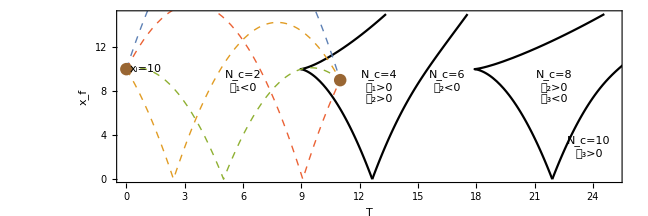

```mathematica
xi=10;
xmax=15;
Clear[findT];    (*---- assume g=1 ----*)
findT[xi_,xf_,1,1]:=Sqrt@Root[-64 xf^3-192 xf^2 xi-192 xf xi^2-64 xi^3+(-60 xf^2+312 xf xi-60 xi^2) #1+(-12 xf-12 xi) #1^2+#1^3&,1];
findT[xi_,xf_,n_,nroot_]:=Sqrt@
Root[-256 n^2 xf^4+256 n^4 xf^4+1024 n^2 xf^3 xi-3072 n^4 xf^3 xi+2048 n^6 xf^3 xi-1536 n^2 xf^2 xi^2+5632 n^4 xf^2 xi^2-8192 n^6 xf^2 xi^2+4096 n^8 xf^2 xi^2+1024 n^2 xf xi^3-3072 n^4 xf xi^3+2048 n^6 xf xi^3-256 n^2 xi^4+256 n^4 xi^4+(-320 n^2 xf^3+256 n^4 xf^3+320 n^2 xf^2 xi+512 n^4 xf^2 xi-1024 n^6 xf^2 xi+320 n^2 xf xi^2+512 n^4 xf xi^2-1024 n^6 xf xi^2-320 n^2 xi^3+256 n^4 xi^3) #1+(4 xf^2-128 n^2 xf^2+64 n^4 xf^2-8 xf xi+64 n^2 xf xi+256 n^4 xf xi+4 xi^2-128 n^2 xi^2+64 n^4 xi^2) #1^2+(4 xf-16 n^2 xf+4 xi-16 n^2 xi) #1^3+#1^4&,nroot];
grPD=ParametricPlot[{
{findT[xi,xf,1,1],xf},
{findT[xi,xf,2,1],xf},
{findT[xi,xf,2,2],xf},
{findT[xi,xf,3,1],xf},
{findT[xi,xf,3,2],xf}
},{xf,0,xmax},
PlotRange->{{0,25},{0,15}},PlotRangePadding->0,PlotStyle->Black,
ImageSize->{648,216},AspectRatio->Full,FrameLabel->{"T","x_f"},
ImagePadding->{{Automatic,Automatic},{Automatic,4}},
Epilog->{
{
Text["N_c=2\n𝒟_1<0",{6,10},{0,1}],
Text["N_c=4\n𝒟_1>0\n𝒟_2>0",{13,10},{0,1}],
Text["N_c=6\n𝒟_2<0",{16.5,10},{0,1}],
Text["N_c=8\n𝒟_2>0\n𝒟_3<0",{22,10},{0,1}],
Text["N_c=10\n𝒟_3>0",{23.8,4},{0,1}]
}//Style[#,16]&,
Text["x_i=10",{1,xi}]
}];
grPaths=plotPathsXf[10,9,11,1,1,1,{AbsoluteThickness@1,Dashed}&];
grCombined=Show[grPD,grPaths,PlotRangeClipping->True]
```

```mathematica
Export[ParentDirectory@NotebookDirectory[]<>"/TEX/Bouncer1PhaseDiagram.pdf",grCombined];
```

### Section.Subsection Phase diagram as function of (x_i,x_f) for fixed T

In this section, we analyze the quartic equation to obtain the number of physically meaningful solutions.  Examine the discriminant:

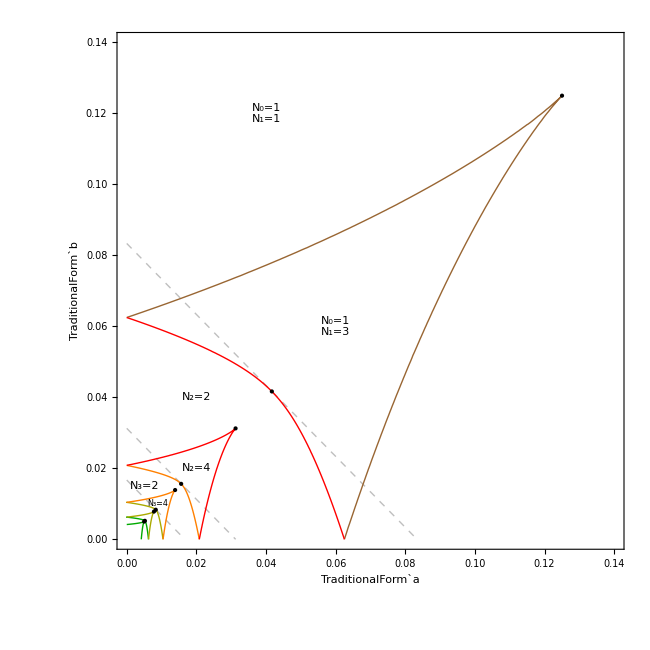

```mathematica
Clear[a,b,n,u,discrim4];
discrim[n_,a_,b_]=Discriminant[1-4 a+4 a^2+4 b-8 a b+4 b^2-16 a n^2-32 a^2 n^2+32 a b n^2+64 a^2 n^4+(-4+8 a-8 b+32 a n^2) u+(4-8 n^2-48 a n^2+16 b n^2+64 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4,u]/65536;
cpOpts={PlotRange->All,ContourShading->None,MaxRecursion->3};
gr=Show[
(*-------- DASHED LINES: STRAIGHT LINE APPROXIMATION --------*)
ContourPlot[√(1+1/(4(a+b))),{a,0,.2},{b,0,.2},Contours->{1,2,3,4},ContourStyle->{{Dashed,GrayLevel@.75}},cpOpts//Evaluate],
(*-------- ZERO CONTOURS OF DISCRIMINANTS FOR n=1,2,3,4,5 --------*)
ContourPlot[discrim[1,a,b],{a,0,1/8},{b,0,1/8},Contours->{0},ContourStyle->resistorColorList⟦2⟧,cpOpts//Evaluate],
Table[
ContourPlot[discrim[n,a,b],{a,0,1/(8n(n-1))},{b,0,1/(8n(n-1))},Contours->{0},ContourStyle->resistorColorList⟦1+n⟧,cpOpts//Evaluate]
,{n,{5,4,3,2}}],
(*-------- OTHER ANNOTATIONS --------*)
Graphics[{AbsolutePointSize@3,Table[Point@{1/(8 n^2),1/(8 n^2)},{n,1,5}],Table[Point@{1/(8(n^2-1)),1/(8(n^2-1))},{n,2,5}],
Text["N_0=1\nN_1=1",{.04,.12}],Text["N_0=1\nN_1=3",{.06,.06}],Text["N_2=2",{.02,.04}],
Text["N_2=4",{.02,.02}],Text["N_3=2",{.005,.015}],Text["N_3=4"//Style[#,8]&,{.009,.01}]
}//Style[#,FontFamily->"Times"]&],
PlotRange->{{0,1},{0,1}}*0.14,RotateLabel->False,LabelStyle->{Black,12,FontFamily->"Times"},PlotRangePadding->0,
ImageSize->650,
FrameLabel->{"TraditionalForm`a","TraditionalForm`b"}]//
Legended[#,Placed[#,{.9,.5}]&@LineLegend[Rest@resistorColorList,{"D_1=0","D_2=0","D_3=0","D_4=0"},LabelStyle->{Black,14,FontFamily->"Times"}]]&
```

```mathematica
(*Export[NotebookDirectory[]<>"/PhaseDiagram.pdf",gr];*)
```

Number of parameters:  The classical bouncer has only two dimensionless parameters, which are the scaled initial and final altitudes a and b.

Discriminant study:  The figure above shows zero contours of the discriminant of the quartic polynomial in the equation for the initial velocity v_i=ugT as a function of the initial altitude x_i=ag T^2 and final altitude x_f=bg T^2, for various values of n (the number of bounces).  The regions of the phase diagram are labeled with the numbers of paths for the largest number of bounces.  For example, in the region labeled “N_3=2”, the path counts are N_0=1 (one direct path), N_1=3 (three single-bounce paths), N_2=4 (four double-bounce paths), and N_3=2 (two triple-bounce paths).

Existence of solutions for n=0 and n=1
It is always possible to find a direct path from x_i to x_f in time T with zero bounces, by throwing the ball up into the air.
It is always possible to find a path from x_i to x_f in time T with one bounce, by throwing the ball against the ground.
For large values of x_i and x_f, these are the only two solutions.

Extra solutions
As x_i and x_f are reduced (or as T increases), the number of possible paths increases.  Every time the discriminant of a polynomial crosses zero, the number of roots of that polynomial increases by two.  For example, to the bottom left of the brown curve, there are three single-bounce solutions with n=1.  Going further to the bottom left, two double-bounce solutions appear, followed by two more to make a total of four double-bounce solutions.  The pattern appears roughly self-similar.

To get more insight, consider symmetrical trajectories where x_i=x_f, that is, a=b.  The discriminant simplifies to D=65536 n^4 ((8a n^2-1)^3 [(4+8a)n^2-1])^2 [8a(n^2-1)-1].  For a given value of n, D is a sixth-degree polynomial in a.  D changes sign at a=1/8 n^2 and also at a=1/8(n^2-1).  Thus, for a given value of n, solutions are possible for a≤1/8(n^2-1).  Conversely, for a given value of a, the allowed values of n satisfy n≤√(1+1/8a).  Thus an upper bound on n is n_max=⌈√(1+1/8a)⌉.  Returning to the general case where a≠b, we can construct the tangent to the boundaries by replacing a by (a+b)/2.  This gives us a general upper bound as n_max=⌈√(1+1/4(a+b))⌉.  These lines are the light gray dashed lines in the phase diagram above.

Heuristic arguments
Suppose the initial and final heights x_i and x_f are given, and suppose x_i≥x_f for concreteness.  The overall motion of the particle is slowest if the total energy is as small as possible, in other words, if the particle starts at rest with v_i=0.  Then:
– the duration of the first segment of the trajectory is t_1=√(2x_i/g)
– the time interval between bounces is Δ t_min=√(8x_i/g)
– the duration of the last segment of the trajectory, T-t_n, is between 0 and √(8x_i/g).
In this case, the total time elapsed is T≥√(2x_i/g)+(n-1)√(8x_i/g), that is, T≥(2n-1)√(2x_i/g).  So the number of bounces satisfies n≤T √(g/(8 x_i))+1/2.  If the initial velocity is v_i≠0, then the time between bounces is Δt=(2 √(v_i^2+2g x_i))/g>√(8x_i/g).  It is possible that this increases the number of bounces by 1, but asymptotically, increasing initial speed will reduce the total number of bounces.  In any case, taking T≥(2n-1)√(2x_i/g) and writing x_i=ag T^2, we see that 8 n^2 a<1 (roughly), in agreement with the rigorous bounds derived earlier on.

Summary
If a particle goes from height x_i to height x_f in time T, the maximum number of bounces cannot exceed
	n_max=⌈√(1+1/(4(a+b)))⌉. 
Also, since there are at most four trajectories for each value of n, the maximum number of paths cannot exceed
	N_max=4+4⌈√(1+1/(4(a+b)))⌉.

This means that calculating the propagator of the quantum bouncer using the Feynman path integral should involve a sum over a finite number of paths!  This is in marked contrast to the case of the classical particle-in-a-box bouncing between two hard walls, where there are an infinite number of possible paths.  To calculate the propagator of the particle-in-a-box using the FPI requires an infinite sum (over an infinite number of “images”)!

### Section.Subsection Classical action S_α

#### Action for free-fall path

Consider a free-fall path X(t) with uniform acceleration X^(..)=-g, initial position X(0)=x_i, and initial velocity Ẋ(0)=v_i.  We can solve the ODE to get X(t), and use S=∫dt L to get the action:
	X=x_i+v_i t-(g t^2)/2,
	S=MT/6[2 g^2 T^2+3 v_i^2-6gT v_i-6g x_i].
To get the result in a more symmetrical form, consider a free-fall path X(t) with uniform acceleration X^(..)=-g, initial position X(0)=x_i, and final position X(T)=x_f.  The path is a straight-line path plus a parabola:
	X=x_i+(x_f-x_i)t/T+1/2 gt(T-t)	
	S= M/(2T)(x_f-x_i)^2-MgT/2(x_f+x_i)-(M g^2 T^3)/24.
We will find it useful to eliminate (x_i,x_f,T) and write the action instead in terms of the initial velocity v_i, final velocity v_f, and velocity-at-ground v_m:
	S=M/(6g)[2(v_i^3-v_f^3)-3v_m^2(v_i-v_f)].

#### Code

```mathematica
Clear[T,xf,xi,vi,vf,g,M,vm,X,S]
X[t_]:=xi+vi t-g t^2/2;
S=Integrate[m/2 X'[t]^2-m g X[t],{t,0,T}]//FullSimplify
```

1/6 m T (2 g^2 T^2+3 vi^2-6 g (T vi+xi))

```mathematica
Clear[X,t,T];
X[t_]=X[t]/.DSolve[{X''[t]==-g,X[0]==xi,X[T]==xf},X[t],t]//First//FullSimplify
S=Integrate[m/2 X'[t]^2-m g X[t],{t,0,T}]//FullSimplify
```

1/2 g t (-t+T)+(t (xf-xi))/T+xi

-(m (g^2 T^4-12 (xf-xi)^2+12 g T^2 (xf+xi)))/(24 T)

```mathematica
X[t_]=1/2 g t (-t+T)+(t (xf-xi))/T+xi/.{xi->(vm^2-vi^2)/(2g),xf->(vm^2-vf^2)/(2g),T->(vi-vf)/g}//FullSimplify
S=Integrate[m/2 X'[t]^2-m g X[t],{t,0,T}]/.{xi->(vm^2-vi^2)/(2g),xf->(vm^2-vf^2)/(2g),T->(vi-vf)/g}//FullSimplify
```

(-(-g t+vi)^2+vm^2)/(2 g)

(m (-2 vf^3+2 vi^3+3 (vf-vi) vm^2))/(6 g)

#### Action due to a bounce

Let us temporarily consider a slightly more sophisticated problem.  Consider a particle that bounces off a surface that exerts a constant restoring force λMg, where λ≫1, according to the potential energy function,
	V(x)=Piecewise[{{λMg|x|, x<0}, {Mgx, x>0,}}]
where the particle has initial position x_i=h and initial velocity is v_i=0, and the final time is T=2 √((2h)/g).  The trajectory consists of three parabolic segments, as illustrated below:

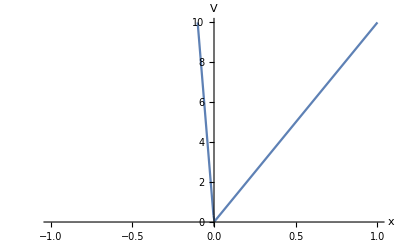
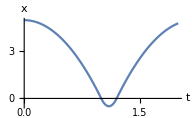
-Graphics-		-Graphics-	
	Soft Classical Bouncer: Potential				Trajectory

The particle first hits the surface x=0 at t=t_2=√(2h/g).  The action for the first part of the trajectory is thus
	S_falling=-(M g^2 t_2^3)/24+ M/(2 t_2)(0-h)^2-(Mg t_2)/2(0+h)
		  =-(M g^2)/24((2h)/g)^(3/2)+ (M  h^2)/(2 √(2h/g))-(Mg √(2h/g))/2 h
		  =-(√(2 M^2 g h^3))/3.
The particle remains below the surface until time t_3=√(2h/g)+2/λ √(2h/g).  During this time, the effective gravitational field strength is g_eff=-λg.  The action accumulated is
	S_submerged=-((M(-λg))^2 (t_3-t_2)^3)/24+M/(2 (t_3-t_2))(0-0)^2-(M(-λg)(t_3-t_2))/2(0+0)
			=-(λ^2 M g^2 (2/λ √(2h/g))^3)/24
			=-(2 √(2 M^2 g h^3))/(3λ)
∴	lim_(λ→∞) S_submerged=0.
The action for the final part of the trajectory is approximately the same as for the first part,
	S_falling≈-(√(2 M^2 g h^3))/3.
There is a discrepancy because the final point is not the same.  But in the limit λ→∞ the path becomes symmetrical and
	lim_(λ→∞) S_falling=0.
The above argument shows that the short time interval t_2<t<t_3 contributes zero to the classical action in the limit λ→∞.  Therefore, there is zero “bounce action” insofar as pure classical mechanics is concerned.

As noted in the literature (Goodman 1981, Schulman, …), in the quantum-mechanical problem, there is a π phase change (or -1 phase factor) associated with each bounce.  This corresponds to an action ΔS=±h/2=±πℏ.  This is beyond the classical analysis above.  We will insert the –1 factor later on.

#### Action for multi-bounce path

Consider an n-bounce path consisting of segments as follows:
(a)  1 segment starting at speed v_i and ending at speed 0
(b)  n segments starting at speed 0 and ending at speed -v_m
(c)  n segments starting at speed +v_m and ending at speed 0
(d)  1 segment starting at speed 0 and ending at speed v_f (assuming v_f<0)
The total action is a sum of terms of the form S_β=M/(6g)[2(v_βi^3-v_βf^3)-3v_βm^2(v_βi-v_βf)]:
	S=M/(6g)[2(v_i^3-0)+3v_m^2(0-v_i)]+2nM/(6g)[0-2(-v_m)^3+3v_m^2((-v_m)-0)]+M/(6g)[2(0-v_f^3)+3v_m^2(v_f-0)]
	  =M/(6g)[2 v_i^3-3 v_m^2 v_i]-2n M/(6g)v_m^3+M/(6g)[-2 v_f^3+3 v_m^2 v_f]
	  =M/(6g)[2(v_i^3-v_f^3)-3v_m^2(v_i-v_f)-2n v_m^3].

For the classical bouncer, the action along a stationary path is
	S(v_i,v_f,v_m,n)=M/(6g)[2(v_i^3-v_f^3)-3v_m^2(v_i-v_f)-2n v_m^3].

This is a formula for the action in terms of the initial and final velocities, the maximum velocity (which is the same for each segment), and n.  This form is nice because there are no square roots.  Note that S_multibounce=S_freefall-n(M v_m^3)/(3g).

We can also use this formula to calculate the cumulative action along a path for given x_i and v_i:
	S(t)=M/(6g)[2(v_i^3-v_f^3)-3v_m^2(v_i-v_f)-2n v_m^3]  where v_m=√(v_i^2+2g x_i), n=⌊(gt-v_i)/(2 v_m)+1/2⌋, v_f=v_i-gT+2n v_m.

In terms of dimensionless variables u=v_i/gT, v=v_f/gT, and w=v_m/gT,
	S=(M g^2 T^3)/6[2(u^3-v^3)-3w^2(u-v)-2n w^3].
Later on, it will be convenient to use v=u-1+2nw and w=√(u^2+a) to obtain S as a function of n, a, and u only:
	S=(M g^2 T^3)/6[2+3a-24a n^2-6u+24a n^2 u+3 u^2+24 n^2 u^2-24 n^2 u^3+(-12n-4an+16a n^3+24nu-8n u^2-16 n^3 u^2) √(u^2+a)].

#### Code

```mathematica
Clear[T,xf,xi,vi,vf,g,M,vm,X,S]
X[t_]:=xi+vi t-g t^2/2;
```

```mathematica
S=Integrate[m/2 X'[t]^2-m g X[t],{t,0,T}]//FullSimplify
S=S/.Solve[X[T]==xf,vi]//First//FullSimplify   (*---- S(xi,xf,T) ----*)
S=S/.{xi->(vm^2-vi^2)/(2g),xf->(vm^2-vf^2)/(2g),T->(vi-vf)/g}//FullSimplify  (*---- S(vi,vf,vm) ----*)
```

1/6 m T (2 g^2 T^2+3 vi^2-6 g (T vi+xi))

-(m (g^2 T^4-12 (xf-xi)^2+12 g T^2 (xf+xi)))/(24 T)

(m (-2 vf^3+2 vi^3+3 (vf-vi) vm^2))/(6 g)

```mathematica
Clear[u,v,w,a];
2(u^3-v^3)-3 w^2(u-v)-2n w^3/.v->u-1+2n w/.{w->√(u^2-a)}//Expand//FullSimplify
%/.{u^2-a->w^2}//PowerExpand//Collect[#,u]&//Collect[#,w]&
```

2-24 n^2 u^3-12 n √(-a+u^2)+6 u (-1+4 n √(-a+u^2))+a (3+4 n (6 n (-1+u)-√(-a+u^2)+4 n^2 √(-a+u^2)))+u^2 (3-8 n (√(-a+u^2)+n (-3+2 n √(-a+u^2))))

2+3 a-24 a n^2-6 u+24 a n^2 u+3 u^2+24 n^2 u^2-24 n^2 u^3+(-12 n-4 a n+16 a n^3+24 n u-8 n u^2-16 n^3 u^2) w

```mathematica
(*2(u^3-v^3)-3 w^2(u-v)-2n w^3/.w->(v-u+1)/(2n)//FullSimplify*)
```

```mathematica
Clear[x,X,xi,u,t,g,S,m];
```

#### Some graphics

```mathematica
Clear[h,g];
-(m g^2)/24((2h)/g)^(3/2)+ (m  h^2)/(2 √(2h/g))-(m g √(2h/g))/2 h//FullSimplify//PowerExpand//FullSimplify
```

```mathematica
h=5;g=10;λ=10;m=1;
Plot[Piecewise[{{-λ m g x, x<0}, {m g x, x>0}}],{x,-5,5},AxesLabel->{"x","V"},PlotRange->{{-1,1},{0,10}}]
```

```mathematica
h=5;g=10;λ=10;
Plot[
Piecewise[{{h-(g t^2)/2, t≤√(2h/g)}, {-g √(2h/g)(t-√(2h/g))+(λ g)/2(t-√(2h/g))^2, √(2h/g)<t<√(2h/g)(1+2/λ)}, {g √(2h/g)(t-√(2h/g)(1+2/λ))-g/2(t-√(2h/g)(1+2/λ))^2, True}}]
,{t,0,2 √(2h/g)},AxesLabel->{"t","x"}]
```

### Section.Subsection Van Vleck determinant D_α

#### Calculating (∂v_i)/(∂x_i), (∂v_i)/(∂x_f), and (∂^2 S)/(∂x_i∂x_f)

Equation for v_i:  In the section on “Relation between time of flight T and initial velocity v_i” we showed that
	2k(u-1)√(u^2+a)+k^2 u^2-2u+(k^2-1)a+b+1=0.

Equations for (∂v_i)/(∂x_i) and (∂v_i)/(∂x_f):  Starting with the equation above, perform implicit differentiation, assuming that k is a constant.  We obtain
	2k[du √(u^2+a)+(u-1)(1/2(2u du+da)/(√(u^2+a)))]+(2 k^2 u-2)du+(k^2-1)da+db=0
∴	2k √(u^2+a)du+(2ku(u-1) du)/(√(u^2+a))+(k(u-1) da)/(√(u^2+a))+(2 k^2 u-2)du+(k^2-1)da+db=0
∴	[2k √(u^2+a)+(2ku(u-1))/(√(u^2+a))+2 k^2 u-2]du+[(k(u-1))/(√(u^2+a))+k^2-1]da+db=0
∴	(∂u)/(∂a)=-[(k(u-1))/(√(u^2+a))+k^2-1]/[2k √(u^2+a)+(2ku(u-1))/(√(u^2+a))+2 k^2 u-2]
 	(∂u)/(∂b)=-1/[2k √(u^2+a)+(2ku(u-1))/(√(u^2+a))+2 k^2 u-2].
If desired, we can redimensionalize to obtain (∂v_i)/(∂x_i)=2/T(∂u)/(∂a) and (∂v_f)/(∂x_f)=2/T(∂u)/(∂b).

The van Vleck determinant (∂^2 S)/(∂x_i∂x_f):  Recall that the action for the multi-bounce path may be written as S(a,u) where
	S=(M g^2 T^3)/6[2+3a-24a n^2-6u+24a n^2 u+3 u^2+24 n^2 u^2-24 n^2 u^3+(-12n-4an+16a n^3+24nu-8n u^2-16 n^3 u^2) √(u^2+a)].
Treat g, T, and n as constants.  We want to compute |det (∂^2 S)/(∂x_i∂x_f)|.  Since we have a 1D problem, this is just |(∂^2 S)/(∂x_i∂x_f)|.  Using the chain rule,
	(∂S(a,b))/(∂a)=(∂S(a,u))/(∂a)+(∂u)/(∂a)(∂S(a,u))/(∂u)=^def f(a,u).
Differentiate this further with respect to b:
	(∂^2 S)/(∂a∂b)=∂/(∂b)f=(∂u)/(∂b)(∂f)/(∂u).
In this way we obtain a closed-form expression for (∂^2 S)/(∂a∂b) as a function of a and u.  After much manipulation,
	(∂^2 S)/(∂x_i∂x_f)=4/(g^2 T^4)(∂^2 S)/(∂a∂b)
		=M/T w/(2n(a-u)+4n u^2-w+4 n^2 uw) 	where w=√(u^2+a)
		=M/T w^2/(uv+av-bu)				in terms of x_i,x_f,v_i,v_f,v_m
		=M/T(1-u+v)^2/(4 n^2 (uv+av-bu))			in terms of x_i,x_f,v_i,v_f,n
		=M/T w^2/(uv(1+v-u)+(v-u)w^2)		in terms of v_i,v_f,v_m
		=M/T(v-u+1)/(u^2+v^2+v-u+(4 n^2-2)uv)		in terms of v_i,v_f,n.
We have used the relations v=u-1+2nw and w^2=u^2+a=v^2+b above.  We will not write (∂^2 S)/(∂x_i∂x_f) in terms of x_i,x_f,T alone because of the sign ambiguity problem.

Close to a stationary path,
	(∂^2 S)/(∂x_i∂x_f)(v_i,v_f,v_m)=(M v_m^2)/(T v_i v_f+2(x_i v_f-x_f v_i)).

#### Mathematica derivation of (∂v_i)/(∂x_i) and (∂v_i)/(∂x_f)

```mathematica
(*-------- FULLY AUTOMATIC CALCULATION --------*)
2k(u-1)√(u^2+a)+k^2 u^2-2u+(k^2-1)a+b+1        /.{u->u[z],a->a[z],b->b[z]}
D[(%), z] //FullSimplify
dLHS=% /.{a'[z]->da,b'[z]->db,u'[z]->du,a[z]->a,b[z]->b,u[z]->u}
duda=Solve[dLHS==0/.{db->0,da->1},du]//Last//Last//Last//FullSimplify
dudb=Solve[dLHS==0/.{db->1,da->0},du]//Last//Last//Last//FullSimplify
```

1+(-1+k^2) a[z]+b[z]-2 u[z]+k^2 u[z]^2+2 k (-1+u[z]) √(a[z]+u[z]^2)

(-1+k^2) a'[z]+b'[z]-2 u'[z]+2 k^2 u[z] u'[z]+2 k √(a[z]+u[z]^2) u'[z]+(k (-1+u[z]) (a'[z]+2 u[z] u'[z]))/(√(a[z]+u[z]^2))

db-2 du+da (-1+k^2)+2 du k^2 u+(k (-1+u) (da+2 du u))/(√(a+u^2))+2 du k √(a+u^2)

(√(a+u^2)-k (-1+u+k √(a+u^2)))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))

-(√(a+u^2))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))

```mathematica
blah=duda/.√(a+u^2)->w//FullSimplify;
num=blah//Numerator//Expand;
den=blah//Denominator//Expand;
dudaCollected=(num//Collect[#,w]&)/(den//Collect[#,w]&)/.w->√(a+u^2)
dudaCollected-duda//FullSimplify
(*(num*(den/.w->-w)//Expand//(#/.w^2->u^2+a&)//FullSimplify//Collect[#,w]&)/(den*(den/.w->-w)//Expand//(#/.w^2->u^2+a&)//FullSimplify//Collect[#,w]&)/.w->√(a+u^2)//FullSimplify*)
```

(k-k u+(1-k^2) √(a+u^2))/(2 a k-2 k u+4 k u^2+(-2+2 k^2 u) √(a+u^2))

0

```mathematica
blah=dudb/.√(a+u^2)->w//FullSimplify;
num=blah//Numerator//Expand;
den=blah//Denominator//Expand;
dudbCollected=(num//Collect[#,w]&)/(den//Collect[#,w]&)/.w->√(a+u^2)
dudbCollected-dudb//FullSimplify
```

-(√(a+u^2))/(2 a k-2 k u+4 k u^2+(-2+2 k^2 u) √(a+u^2))

0

```mathematica
(*-------- MANUAL ENTERING --------*)
dudaManual=-((k(u-1))/(√(u^2+a))+k^2-1)/(2k √(u^2+a)+(2k u(u-1))/(√(u^2+a))+2 k^2 u-2)//FullSimplify
```

-(-1+k^2+(k (-1+u))/(√(a+u^2)))/(2 (-1+k^2 u+(k (a+u (-1+2 u)))/(√(a+u^2))))

Check that these are the same:

```mathematica
duda-dudaManual//FullSimplify
```

0

#### Mathematica derivation of (∂^2 S)/(∂x_i∂x_f)

```mathematica
Clear[a,b,g,T,xi,xf,vi,vf,vm,u,v,w,n,M];
SSS=M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)/.{vf->vi-g T+2n vm}//FullSimplify;
SSS=SSS/.{vm->√(vi^2+2g xi),vf->√(vi^2+2g (xi-xf))}//FullSimplify;
SSS=SSS/.{xi->a(g T^2)/2,xf->b(g T^2)/2,vi->u g T}//FullSimplify//PowerExpand//FullSimplify
```

-1/6 g^2 M T^3 (-2+3 a (1+8 n^2 (-1+u))+3 u (2+(-1+8 n^2 (-1+u)) u)+4 n √(a+u^2) (3+a (-1+4 n^2)+2 u (-3+u+2 n^2 u)))

```mathematica
duda=(√(a+u^2)-k (-1+u+k √(a+u^2)))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))/.k->2n//FullSimplify
dudb=-(√(a+u^2))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))))/.k->2n//FullSimplify
dSda=D[SSS, a]+duda*D[SSS, u]//Simplify
dSdbda=dudb*D[dSda, u]//Simplify
dSdxidxf=4/(g^2 T^4)dSdbda//FullSimplify
```

(√(a+u^2)-2 n (-1+u+2 n √(a+u^2)))/(-2 √(a+u^2)+4 n (a+u (-1+2 u+2 n √(a+u^2))))

-(√(a+u^2))/(-2 √(a+u^2)+4 n (a+u (-1+2 u+2 n √(a+u^2))))

-1/2 g^2 M T^3 u

(g^2 M T^3 √(a+u^2))/(2 (-2 √(a+u^2)+4 n (a+u (-1+2 u+2 n √(a+u^2)))))

(M √(a+u^2))/(T (-√(a+u^2)+2 n (a+u (-1+2 u+2 n √(a+u^2)))))

```mathematica
T/M dSdxidxf/.{n->(v-u+1)/(2w)}/.{u->√(w^2-a),v->√(w^2-b)}//Simplify//PowerExpand//FullSimplify
%/.{√(w^2-a)->u,√(w^2-b)->v}//Factor
```

w^2/(-b √(-a+w^2)+√(-b+w^2) (a+√(-a+w^2)))

-w^2/(b u-a v-u v)

```mathematica
-w^2/(b u-a v-u v)/.w->(v-u+1)/(2n)//FullSimplify
```

-(1-u+v)^2/(4 n^2 (b u-(a+u) v))

#### TeXing: duda, dudb, S(u,a)

```mathematica
duda=dudaCollected/.k->2n
dudb=dudbCollected/.k->2n
```

(2 n-2 n u+(1-4 n^2) √(a+u^2))/(4 a n-4 n u+8 n u^2+(-2+8 n^2 u) √(a+u^2))

-(√(a+u^2))/(4 a n-4 n u+8 n u^2+(-2+8 n^2 u) √(a+u^2))

```mathematica
(2 n(1-u)-(4 n^2-1) √(a+u^2))/(4 n (a-u+2 u^2)+2(4 n^2 u-1)√(a+u^2))-duda//Simplify
```

0

```mathematica
(-√(a+u^2))/(4 n (a-u+2 u^2)+2(4 n^2 u-1) √(a+u^2))-dudb//Simplify
```

```mathematica
0
```

```mathematica
(2 n(1-u)-(4 n^2-1) √(a+u^2))/(4 n (a-u+2 u^2)+2(4 n^2 u-1)√(a+u^2))//TeXForm
```

\frac{2 n (1-u)-\left(4 n^2-1\right) \sqrt{a+u^2}}{2 \sqrt{a+u^2} \left(4 n^2 u-1\right)+4 n \left(a+2 u^2-u\right)}

```mathematica
(-√(a+u^2))/(4 n (a-u+2 u^2)+2(4 n^2 u-1) √(a+u^2))//TeXForm
```

-\frac{\sqrt{a+u^2}}{2 \sqrt{a+u^2} \left(4 n^2 u-1\right)+4 n \left(a+2 u^2-u\right)}

```mathematica
Clear[a,b,g,T,xi,xf,vi,vf,vm,u,v,w,n,M];
SSS=M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)/.{vf->vi-g T+2n vm}//FullSimplify;
SSS=SSS/.{vm->√(vi^2+2g xi),vf->√(vi^2+2g (xi-xf))}//FullSimplify;
SSS=SSS/.{xi->a(g T^2)/2,xf->b(g T^2)/2,vi->u g T}//FullSimplify//PowerExpand//FullSimplify;
(*SSS=SSS/.√(a+u^2)->w//Collect[#,w]&*)
SSS=SSS//Collect[#,√(a+u^2)]&
blah=%/((M g^2 T^3)/6)//Simplify//Collect[#,√(a+u^2)]&
```

-1/6 g^2 M T^3 √(a+u^2) (12 n-4 a n+16 a n^3-24 n u+8 n u^2+16 n^3 u^2)-1/6 g^2 M T^3 (-2+3 a-24 a n^2+6 u+24 a n^2 u-3 u^2-24 n^2 u^2+24 n^2 u^3)

2-3 a+24 a n^2-6 u-24 a n^2 u+3 u^2+24 n^2 u^2-24 n^2 u^3+√(a+u^2) (-12 n+4 a n-16 a n^3+24 n u-8 n u^2-16 n^3 u^2)

```mathematica
(
 2-3 a-6 u+3 u^2+24  n^2(a+u^2)(1-u)+n (-12 +4 a+24  u-8 u^2-16 n^2(a+ u^2))√(a+u^2)       
)-blah//FullSimplify
```

0

```mathematica
2-3 a-6 u+3 u^2+24  n^2(a+u^2)(1-u)+n (-12 +4 a+24  u-8 u^2-16 n^2(a+ u^2))√(a+u^2)       //HoldForm//TeXForm
```

2-3 a-6 u+3 u^2+24 n^2 \left(a+u^2\right) (1-u)+n \left(-12+4 a+24 u-8 u^2-16 n^2 \left(a+u^2\right)\right) \sqrt{a+u^2}

#### Numerical verification

```mathematica
calc˘vi˘n[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{t,t1,Δt,tn,a,b,n,vi,vm,vf,uSols,nα,uα,αmax,nmax,Sα,S},
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];
{nα,uα}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
{uα*g*T,nα}
];
calc˘vi[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
vi
];
calc˘dvidxi[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,u,a,b,k,duda},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];(* note that vi,n,u,vm,vf,S are all vectors *)
u=vi/(g T);a=(2xi)/(g T^2);b=(2xf)/(g T^2);k=2n;duda=(√(a+u^2)-k (-1+u+k √(a+u^2)))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))));2/T duda
];
calc˘dvidxf[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,u,a,b,k,dudb},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
u=vi/(g T);a=(2xi)/(g T^2);b=(2xf)/(g T^2);k=2n;dudb=-(√(a+u^2))/(2 (a k-√(a+u^2)+k u (-1+2 u+k √(a+u^2))));2/T dudb
];
calc˘S[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,vm,vf,S,a,b,u,v,w},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
a=(2xi)/(g T^2);u=vi/(g T);w=√(u^2+a);v=u-1+2n w;S=(M g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2n w^3)
];
calc˘dSdxixdf[xf_,xi_,T_,M_,g_,ℏ_]:=Module[{vi,n,k,u,vm,vf,a,b,v,w,dSdxidxf},
{vi,n}=calc˘vi˘n[xf,xi,T,M,g,ℏ];
a=(2xi)/(g T^2);b=(2xf)/(g T^2);u=vi/(g T);w=√(u^2+a);v=u-1+2n w; dSdxidxf=M/T w^2/(u v+a v-b u)
];
```

Do the verification!

```mathematica
xf=1.;xi=2;T=8;M=g=ℏ=1;
Do[Print@((calc˘vi[xf,xi+dx,T,M,g,ℏ]-calc˘vi[xf,xi,T,M,g,ℏ])/dx),{dx,{.1,.01,.001}}]
Print@calc˘dvidxi[xf,xi,T,M,g,ℏ]
```

{-0.125,0.495133,-0.495662,-0.12447,0.594958,-0.591789}

{-0.125,0.490321,-0.490854,-0.124467,0.586627,-0.583417}

{-0.125,0.48985,-0.490383,-0.124467,0.585819,-0.582605}

{-0.125,0.489798,-0.490331,-0.124467,0.585729,-0.582515}

```mathematica
Do[Print@((calc˘vi[xf+dx,xi,T,M,g,ℏ]-calc˘vi[xf,xi,T,M,g,ℏ])/dx),{dx,{.1,.01,.001}}]
Print@calc˘dvidxf[xf,xi,T,M,g,ℏ]
```

{0.125,-0.170977,0.188539,-0.142561,0.222533,-0.293309}

{0.125,-0.171201,0.187855,-0.141654,0.219858,-0.28402}

{0.125,-0.171224,0.187788,-0.141564,0.219596,-0.283144}

{0.125,-0.171226,0.18778,-0.141554,0.219567,-0.283047}

```mathematica
Do[Print@((calc˘S[xf+dx,xi+dx,T,M,g,ℏ]+calc˘S[xf,xi,T,M,g,ℏ]-calc˘S[xf,xi+dx,T,M,g,ℏ]-calc˘S[xf+dx,xi,T,M,g,ℏ])/dx^2),{dx,{.1,.01,.001}}]
Print@calc˘dSdxixdf[xf,xi,T,M,g,ℏ]
```

{-0.125,0.172863,-0.190359,0.142496,-0.22627,0.296301}

{-0.125,0.171387,-0.188035,0.141647,-0.220211,0.28431}

{-0.125,0.171242,-0.187806,0.141563,-0.219632,0.283173}

{-0.125,0.171226,-0.18778,0.141554,-0.219567,0.283047}

#### Visualization of VVD

Define a grid:

```mathematica
xi=10;
(*xfList=Range[0.0625,15,2*0.0625];*)
xfList=Range[0,15,.02];
TList=Range[0.05,25,2*.05];
```

We could plot the action but let’s not do it, because the plots are not that easy to interpret.

```mathematica
(*Monitor[timeIt[   data=Table[calc˘S[xf,xi,T,1,1,1]//Last,{T,TList},{xf,xfList}]    ],{T,xf}]
gr=myRealPlot[TList,xfList,data,FrameLabel->Reverse@{"T","x_f"},PlotLabel->"Classical action S"]*)
```

If we ignore all phase factors, then the semiclassical propagator would be 
	K_only^amplitude=√(i/(2πℏ))∑_(α=1)^N_paths (-1)^n_α|(∂^2 S_α)/(∂x_i∂x_f)|exp (i S_α)/ℏ
For the purpose of visualization, we’ll compute ∑_□  add the VVDs up for ALL paths:

```mathematica
Monitor[timeIt[   data=Table[  Total@Abs@calc˘dSdxixdf[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]    ],{T,xf}]
```

Absolute time = 308.    CPU time = 296.

Absolute time = 272.    CPU time = 270.

Absolute time = 305.    CPU time = 293.

Absolute time = 58.5    CPU time = 52.7

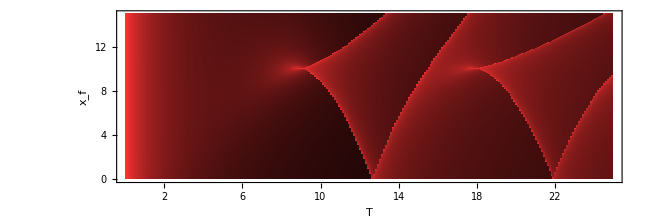

```mathematica
gr=myRealPlot[TList,xfList,1*Abs@data,FrameLabel->Reverse@{"T","x_f"}]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/TEX/Bouncer1VVD.png",gr];
```

### Section.Subsection Infographic

#### Code (run this!)

```mathematica
(*-------- NUMBER OF FOCI BEFORE TIME T --------*)
findMorseIndexM[T_,vi_]:=Module[{vm,n,j,k,m},
vm=√(vi^2+2 g xi);
n=Floor[(g T-vi)/(2vm)+1/2];(* number of bounces *)
j=Floor[(g T-vi)/(2vm)]+UnitStep[vi];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√(g xi)-vi √(2j(j+1))];
m=j+UnitStep[T-(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm)]+2n; (* note the n *)
Return[m]];

analyze[xi_,xf_,T_,g_]:=Module[{a,b,uSols,nmax,n,viα,u,v,w,SαOverM,DαOverM,mα},
a=(2 xi)/(g T^2);b=(2 xf)/(g T^2);nmax=Ceiling[√(1+1/(2 a+2 b))];
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
viα=u g T;
w=√(u^2+a);v=u-1+2n w;
SαOverM=(g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2n w^3);
DαOverM=1/T w^2/(u v+a v-b u);
mα=findMorseIndexM[T,#]&/@viα;
{viα,SαOverM,DαOverM,mα}
];
findBounces[xi_,vi_,T_,g_]:=Module[{tb,t0,vm,n},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;n=Floor[(T-t0)/tb+1/2];t0+(Range[n]-1/2)tb
];
findFoci[xi_,vi_,T_,g_]:=Module[{vm,n,k0Floor,tF,xF,t0,tb,tFxFk},
vm=√(vi^2+2g xi);k0Floor=Floor[1/2(1-vm/vi)];n=⌈(g T-vi)/(2vm)⌉;t0=vi/g;tb=(2vm)/g;
tFxFk={};
Do[        
If[k==k0Floor,Continue[]];
tF=(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm);
xF=(vm^2/(2g)-g/2(tF-t0-tb Floor[(tF-t0)/tb+1/2])^2);
If[tF>T,Continue[]];
AppendTo[tFxFk,{tF,xF}];
,{k,n}];
Return[tFxFk];
];
findXf[xi_,vi_,t_,g_]:=Module[{tb,t0,vm},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;
vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2
];
plotPathVi[xi_,vi_,T_,g_,style_:Directive[AbsoluteThickness@0,Opacity[0.25,Black]] ]:=Module[{vm,xt,tb,t0,αmax,colorα},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;     (* vm and tb are lists *)
xt=Function[{t},vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2];
Plot[Evaluate[xt[t]],{t,0,T},PlotStyle->style,Exclusions->None]];
plotPathWithWiggles[xi_,vi_,T_,g_,amp_:0.1,color_:Gray ]:=Module[{vm,xt,St,θt,M=1,ℏ=1,t,tb,t0,αmax,colorα},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;     (* vm and tb are lists *)
xt[t_]=vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2;
St[t_]:=Module[{n,vf},n=Floor[(t-t0)/tb+1/2];vf=vi-g t+2n vm;M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)];
θt[t_]:=St[t]/ℏ+findMorseIndexM[t,vi];
Plot[{xt[t],xt[t]+amp*Cos[θt[t]](*,xt[t]+amp*Sin[θt[t]]*)},{t,0,T},
PlotStyle->{
{AbsoluteThickness@1,color},
{AbsoluteThickness@2,Lighter[color,.5]},
{AbsoluteThickness@2,CapForm@"Butt",AbsoluteDashing@{1,1},Lighter[color,.5]}},
Exclusions->None]];
```

#### Make the plots

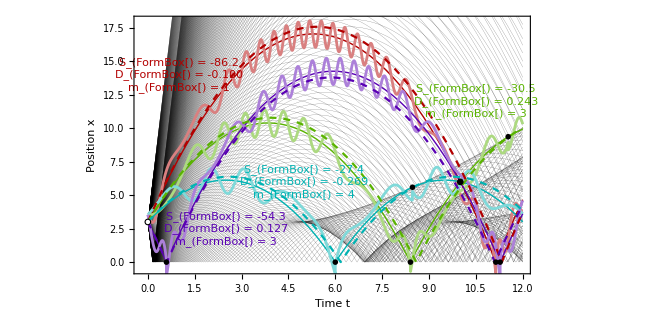

```mathematica
xi=3;   (* initial position *)
viList=Range[-20,20,.1];  (* list of initial velocities for plotting *)
xf=6;   (* final position *)
T=10;   (* final time *)
g=1;
dvi=0.1; (* perturbation of initial velocity *)
Tmax=12; (* maximum time for plotting *)
xmax=18; (* maximum position for plotting *)
wiggleAmp=1;
(*-------- FIND ALLOWED INITIAL VELOCITIES --------*)
{viα,SαOverM,DαOverM,mα}=Transpose@Reverse@Sort@Transpose@analyze[xi,xf,T,g];
αmax=Length@viα;colorα=Hue[#,1,.7]&/@(Range[0,αmax-1]/αmax)//N;
(*-------- UTILITIES --------*)
gpStar=Line@{{{-1,0},{1,0}},{{0,-1},{0,1}},{{-.71,-.71},{.71,.71}},{{-.71,.71},{.71,-.71}}};
gpDiamond=Line@{{1,0},{0,1},{-1,0},{0,-1},{1,0}};
myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
gr=Show[
(*-------- BACKGROUND PATHS --------*)
Table[    plotPathVi[xi,vi,Tmax,g,Directive[AbsoluteThickness@0.1,Black]]    ,{vi,viList}],
(*-------- CLASSICAL PATHS --------*)
(*Table[    plotPathVi[xi,viα⟦α⟧,Tmax,g,colorα⟦α⟧]    ,{α,αmax}],*)
Table[    plotPathWithWiggles[xi,viα⟦α⟧,Tmax,g,wiggleAmp,colorα⟦α⟧]    ,{α,αmax}],
(*-------- PERTURBED PATHS --------*)
Table[    plotPathVi[xi,viα⟦α⟧+dvi,Tmax,g,{Dashed,colorα⟦α⟧}]    ,{α,αmax}],
(*Table[    plotPathVi[xi,viα⟦α⟧-dvi,Tmax,g,{Dashed,colorα⟦α⟧}]    ,{α,αmax}],*)
(*-------- OTHER GRAPHICS --------*)
Graphics[{
(*-------- START AND END POINTS --------*)
Inset[Graphics[{FaceForm[White],EdgeForm@{Thick,Black},Disk[]}],{0,xi},{0,0},Scaled@.05],
Inset[Graphics[{FaceForm[Black],EdgeForm[Black],Disk[]}],{T,xf},{0,0},Scaled@.05]
,
(*-------- BOUNCES --------*)
Table[
tFxFk=findBounces[xi,viα⟦α⟧,Tmax,g];  (* let's plot all the way*)
Inset[Graphics[{colorα⟦α⟧,AbsoluteThickness@2,gpDiamond}],{#,0},{0,0},Scaled@.05]&/@tFxFk
  ,{α,αmax}],
(*-------- FOCI --------*)
Table[
tFxFk=findFoci[xi,viα⟦α⟧,Tmax,g];  (* let's plot all the way*)
Inset[Graphics[{colorα⟦α⟧,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk
  ,{α,αmax}],
(*-------- ACTIONS --------*)
Table[{   
(*tLabel=0.3Tmax;
xLabel=Rescale[α,{.5,αmax+.5},{+1.1xmax,0}];*)
{tLabel,xLabel}=({{1, 14}, {10.5, 12}, {5, 6}, {2.5, 2.5}})⟦α⟧;
colorα⟦α⟧,
Text[
StringForm["S_(``) = ``\nD_(``) = ``\nm_(``) = ``",
α,SαOverM⟦α⟧//NumberForm[#,{∞,1}]&,
α,DαOverM⟦α⟧//NumberForm[#,{∞,3}]&,
α,mα⟦α⟧
]
//myFrameTranslucent,
{tLabel,xLabel},
{0,0}]
},{α,αmax}]
}
],
Frame->True,FrameLabel->{"Time t","Position x"},RotateLabel->True,
PlotRange->{{-.2,Tmax},{-.5,xmax}},PlotRangePadding->0,(*PlotRangeClipping->False,*)
ImageSize->{648,324},AspectRatio->Full,
AxesOrigin->{0,0},Axes->True,
ImagePadding->{{Automatic,Automatic},{Automatic,4}}]
```

```mathematica
Export[ParentDirectory@NotebookDirectory[]<>"/TEX/Bouncer1Everything.png",gr//Rasterize[#,ImageResolution->300]&];
```

### Section.Subsection Compare PI and EE color maps

### Section.Subsection Heatmaps of KPI and KEE

```mathematica
(*-------- USER-DEFINED PARAMETERS --------*)
xi=10;
xfList=Range[0,15,0.03125]; (* fine position grid *)
TList=Range[0.03125,25,0.03125]; (* fine time grid *)
(*xi=10;
xfList=Range[0,15,8*0.0625]; (* coarse grid *)
TList=Range[0.03125,25,8*0.03125];*)
```

```mathematica
timeIt[
dataKEE=KEE[xfList,xi,TList,1,1,1]        ];
```

Absolute time = 49.7    CPU time = 50.1

```mathematica
Monitor[timeIt[
dataVVD=Table[KPIAmplitudeOnly[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]        ],{T,xf}];
```

Absolute time = 658.    CPU time = 649.

```mathematica
Monitor[timeIt[
dataKPI=Table[KPI[xf,xi,T,1,1,1],{T,TList},{xf,xfList}]        ],{T,xf}];
```

Absolute time = 737.    CPU time = 665.

```mathematica
DumpSave[NotebookDirectory[]<>"/bouncer1.mx",{xi,TList,xfList,dataKEE,dataVVD,dataKPI}];
```

```mathematica
(*Get[NotebookDirectory[]<>"/bouncer1.mx"];
Dimensions@dataKPI*)
```

```mathematica
scalFac=2;
grPI=myComplexPlot[TList,xfList,scalFac*dataKPI,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_SCA",Scaled@{0.1,1},{0,1.5}]}];
grEE=myComplexPlot[TList,xfList,scalFac*dataKEE,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_EE",Scaled@{0.1,1},{0,1.5}]}];
grPIMinusEE=myComplexPlot[TList,xfList,scalFac*(dataKPI- dataKEE),FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["K_SCA-K_EE",Scaled@{0.1,1},{0,1.5}]}];
```

```mathematica
gr=YLLGraphicsGrid[
{Reverse@{grPI,grEE,grPIMinusEE}}ᵀ,
ColumnSize->600,(* column size(s) *)
RowSize->108,       (* row size(s) *)
Padding->{{48,8},{48,8}},   (* LRBT paddings to allow space for row and column headings *)
Bleed->48,                 (* bleed in pixels around each panel *)
XLabel->"t",
YLabel->"x_f",
XTicksMain->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->0.003,MinorTickLength->0.002,TickColor->White]&),
XTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->{0,0.003},MinorTickLength->{0,0.002},TickColor->White,TickFormat->None]&),
YTicksMain->(YLLTicks[{#1,14},MajorTickCount->5,MajorTickLength->0.003,MinorTickLength->0.002,TickColor->White]&)
]//Rasterize[#,RasterSize->1024]&
```

-Graphics-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/TEX/Bouncer1Heatmaps.png",gr];
```

```mathematica
scalFac=1;
grVVD=myComplexPlot[TList,xfList,scalFac*dataVVD,FrameLabel->Reverse@{"T","x_f"},Epilog->{White,Text["∑_α √(|SubscriptBox[D, α]|)",Scaled@{0.1,1},{0,1.5}]}];
grVVD
```

-Graphics-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/TEX/Bouncer1VVD.png",gr];
```

### Section.Subsection Slices of KPI and KEE

Choose positions to slice:

```mathematica
nTList=Position[TList,First@Nearest[TList,#]]&/@{9.0,10.0,12.0}//Flatten;

myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
myFrameGray@gr_:=gr//Framed[#,Background->GrayLevel@.8]&;
styleVVD=Directive@{AbsoluteThickness@1,CapForm@"Butt",AbsoluteDashing@{2,2},ColorData[97][4]};
styleKPI=Directive@{AbsoluteThickness@2,CapForm@"Butt",AbsoluteDashing@{3,1},ColorData[97][4]};
styleKEE=Directive@{AbsoluteThickness@1,ColorData[97][1]};
grList=Table[
ListLinePlot[{
{xfList,Abs@dataVVD⟦nT⟧}ᵀ,
{xfList,Abs@dataKPI⟦nT⟧}ᵀ,
{xfList,Abs@dataKEE⟦nT⟧}ᵀ
},
PlotStyle->{styleVVD,styleKPI,styleKEE},
PlotRange->{0,.9},Axes->False,
Epilog->{
Text[StringForm["T=``",TList⟦nT⟧]//Style[#,16]&//myFrameGray,Scaled@{1,1},{+1,1}]
}
],
{nT,nTList}];
```

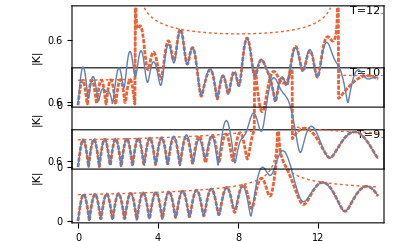

```mathematica
grMat={grList}ᵀ;
gr=YLLGraphicsGrid[
grMat,
ColumnSize->600,(* column size(s) *)
RowSize->108,       (* row size(s) *)
Padding->{{48,8},{48,8}},   (* LRBT paddings to allow space for row and column headings *)
Bleed->48,                 (* bleed in pixels around each panel *)
XLabel->"t",
YLabel->"|K|",
XTicksMain->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->0.003,MinorTickLength->0.002]&),
XTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->{0,0.003},MinorTickLength->{0,0.002},TickFormat->None]&)
]//Legended[#,
LineLegend[{styleVVD,styleKPI,styleKEE},Style[#,{14,FontFamily->"Times"}]&/@{"TraditionalForm`","TraditionalForm`","TraditionalForm`"},
LegendLayout->"Row",LegendMarkerSize->{{30,15}}
]//Placed[#,{{.2,.5},{0,0}}]&]&
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/TEX/Bouncer1Slices.pdf",gr];
```

### Section.Subsection Graphics: paths and actions for given n

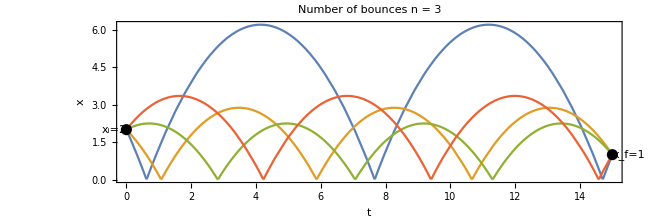

```mathematica
(*-------- USER PARAMETERS --------*)
xi=2;xf=1;T=15;n=3;
g=1;
(*-------- CALCULATE ALLOWED INITIAL VELOCITIES --------*)
a=xi/(g T^2);
b=xf/(g T^2);
Clear[u];
uList=u/.
Solve[1-4 a+4 a^2+4 b-8 a b+4 b^2-16 a n^2-32 a^2 n^2+32 a b n^2+64 a^2 n^4+(-4+8 a-8 b+32 a n^2) u+(4-8 n^2-48 a n^2+16 b n^2+64 a n^4) u^2+16 n^2 u^3+(-16 n^2+16 n^4) u^4==0,u]//N//Select[#,Im@#==0&]&;
viList=uList*g T;
xt[g_,xi_,vi_,t_]:=Module[{t0,τ},t0=vi/g;τ=2/g √(vi^2+2g xi);xi+vi^2/(2g)-g/2(t-t0-τ Floor[(t-t0)/τ+1/2])^2];
Plot[Table[xt[g,xi,vi,t],{vi,viList}]//Evaluate,{t,0,T},
Frame->True,FrameLabel->{"t","x"},ImageSize->{648,216},AspectRatio->Full,PlotRange->{{0,All},All},PlotRangePadding->{{0,0},{0,Scaled@.05}},Axes->None,AxesOrigin->{0,0},ImagePadding->{{48,48},{All,8}},PlotRangeClipping->False,
Epilog->{AbsolutePointSize@8,Black,Point@{0,xi},Point@{T,xf},
Text[StringForm["x_i=``",xi],{0,xi},{+1.5,0}],
Text[StringForm["x_f=``",xf],{T,xf},{-1.5,0}]
},
PlotLabel->StringForm["Number of bounces n = ``",n],
PlotLegends->(StringForm["v_i = ``",#]&/@viList)]
```

```mathematica
(*---- THE FOLLOWING QUANTITIES ARE LISTS ----*)
vi=viList;
xm=xi+vi^2/(2g);
vm=√(vi^2+2g xi);
vf=vi-g T+2n vm;
S=(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)/(6g);
TableForm[
{xm,vi,vm,vf,S}ᵀ,TableHeadings->{None,{"x_m","v_i","v_m","v_f","S"}}
]
```

x_m | v_i | v_m | v_f | S
6.19523 | -2.89663 | 3.52001 | 3.22342 | -24.965
2.87451 | -1.3225 | 2.39771 | -1.93624 | -13.9
2.24669 | 0.702407 | 2.11976 | -1.57904 | -13.2227
3.34763 | 1.64173 | 2.58752 | 2.16686 | -17.4826

```mathematica
Clear[xm,vi,vm,vf,S];
```

### Section.Subsection Graphics: paths for all n – interactive demo

```mathematica
DynamicModule[{tixi={0,10},tfxf={5,9},g=1,xi,xf,T,a,b,nmax,n,u,vi,uSols,viList,αα,xt,αmax,colorαList},
LocatorPane[
(*-------- Constrain locators differently --------*)
Dynamic[{tixi,tfxf},Switch[CurrentValue["CurrentLocatorPaneThumb"],1,tixi⟦2⟧=#⟦1,2⟧,2,tfxf=#⟦2⟧]&],
(*-------- Draw graphics --------*)
Dynamic[
xi=tixi⟦2⟧;xf=tfxf⟦2⟧;T=tfxf⟦1⟧;g=1;
(*-------- CALCULATE NUMBER OF TRAJECTORIES --------*)
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
vi=u g T;
w=√(u^2+a);
v=u-1+2n w;
αmax=Length@n;
αα=Range@αmax;
(*-------- CALCULATE TRAJECTORIES --------*)
xt[t_,vi_]:=Module[{vmax,n,tn},vmax=√(vi^2+2g xi);n=Floor[(g t-vi+vmax)/(2vmax)];tn=(vi-vmax)/g+n*(2vmax)/g;vmax(t-tn)-g/2 (t-tn)^2];
αmax=Length@αα;
colorαList=Hue[#,1,.7]&/@(Range[αmax]/αmax)//N;
(*-------- PLOT --------*)
Plot[
Table[xt[t,vi⟦α⟧],{α,αα}]//Evaluate,{t,0,T},
Frame->True,FrameLabel->{"Time t","Position\nx"},
PlotStyle->Table[Directive@{AbsoluteThickness@0,resistorColorList⟦1+n⟦α⟧⟧},{α,αmax}],
Epilog->{AbsolutePointSize@8,Black,Point@{0,xi},Point@{T,xf},
Text[StringForm["x_i=``",xi],Offset[{10,0},{0,xi}],{-1.,0}],
Text[StringForm["x_f=``",xf],{T,xf},{-1.5,0}]
},ImageSize->{648,324},AspectRatio->Full,PlotRange->{{0,20},{0,40}},PlotRangePadding->{{0,0},{0,0}},AxesOrigin->{0,0},ImagePadding->{{All,64},{All,8}},PlotRangeClipping->False,GridLines->{Range[20],Range[0,40,2]}
]
]
]]
```

Let n be the number of bounces in a path, and let N_n be the number of n-bounce paths.  We see that
	n=0: N_0=1
n=1: N_1=1 or 3
n=2: N_2=0 or 2 or 4
n=3: N_3=0 or 2 or 4
and so on.  The total number of paths, N=N_0+N_1+N_2+…, is a positive even number: N=2,4,6,8,…

```mathematica
Clear[a,b,xi,vi,g,T,vb,n,xt,xf];
```

### Section.Subsection Graphics: paths for all n – static picture

```mathematica
(*-------- CHANGE THESE PARAMETERS IF DESIRED --------*)
xi=1;xf=2;T=9;M=g=ℏ=1;
(*-------- WARNING: n,u,vi,vm,vf,S ARE LISTS! --------*)
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
vi=u g T;
w=√(u^2+a);
v=u-1+2n w;
S=(M g^2 T^3)/6(2(u^2-v^3)-3 w^2(u-v)-2n w^3);
dSdxidxf=M/T w^2/(u v+a v-b u);
αmax=Length@u;αα=Range@αmax;nmax=Max@n;
```

Path index

α | Number of bounces

n | Initial
velocity
v_i | Action

S | Van Vleck
determinant
∂^2 
1 | 0 | 4.61111 | -12.7134 | -0.111111
2 | 1 | -4.39494 | 51.6519 | 0.122608
3 | 1 | 2.17096 | -2.98452 | -0.152014
4 | 1 | 4.14066 | 1.4821 | 0.140517
5 | 2 | -3.86473 | 46.0176 | -0.165312
6 | 2 | -1.94244 | 4.6221 | 0.203385

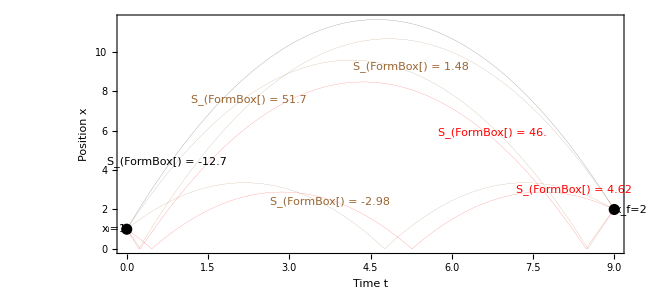

```mathematica
(*-------- CALCULATE TRAJECTORIES --------*)
xt[t_,vi_]:=Module[{vm,τ,n,t0},vm=√(vi^2+2g xi);τ=(2vm)/g;t0=vi/g;
vm^2/(2g)-g/2(t-t0-τ Floor[(t-t0)/τ+1/2])^2];
colorαList=Hue[#,1,.7]&/@(Range[αmax]/αmax)//N;
myTable=TableForm[{αα,n,vi,S,dSdxidxf}ᵀ,TableHeadings->{None,{"Path index\n\nα","Number of bounces\n\nn","Initial\nvelocity\nv_i","Action\n\nS","Van Vleck\ndeterminant\n∂^2 "}}]
gr=Plot[
Table[xt[t,vi⟦α⟧],{α,αα}]//Evaluate,{t,0,T},
Frame->True,FrameLabel->{"Time t","Position\nx"},
PlotStyle->Table[Directive@{AbsoluteThickness@0,resistorColorList⟦1+n⟦α⟧⟧},{α,αmax}],PlotRange->All,
PlotLegends->(Placed[#,{.92,.7}]&@LineLegend[resistorColorList⟦1;;nmax+1⟧,Table[StringForm["n=``",n],{n,0,nmax}],LegendLabel->"Number of\n  bounces\n"]),
Epilog->{AbsolutePointSize@8,Black,Point@{0,xi},Point@{T,xf},
Text[StringForm["x_i=``",xi],{0,xi},{+1.5,0}],
Text[StringForm["x_f=``",xf],{T,xf},{-1.5,0}],
Table[{   resistorColorList⟦1+n⟦α⟧⟧,Text[StringForm["S_(``) = ``",α,S⟦α⟧//NumberForm[#,3]&],{((α-.5) T)/αmax,xt[((α-.5) T)/αmax,vi⟦α⟧]},{0,-1}]   },{α,αmax}]
},ImageSize->{650,300},AspectRatio->Full,PlotRange->All,PlotRangePadding->{{0,0},{0,Scaled@.1}},AxesOrigin->{0,0},ImagePadding->{{All,64},{All,8}},PlotRangeClipping->False,PlotPoints->400
]
```

The different-colored curves show trajectories starting at (0,x_i) and ending at (T,x_f) with n bounces.  In the table above, α is the path number, n is the number of bounces, and v_i is the initial upward velocity for that path.

```mathematica
Clear[xi,viα,g,T,vb,n,xt,xf];
```

```mathematica
(*√(I/(2π ℏ))Total[(-1)^n*√Abs[dSdxidxf]*Exp[(I*S)/ℏ]]*)
```

### Section.Subsection Supplemental visualization: Paths, caustics, focal points

```mathematica
myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
plotPathsVi[xi_,vi_,T_,M_,g_,ℏ_]:=Module[{vm,xt,τ,t0},
vm=√(vi^2+2 g xi);τ=(2 vm)/g;t0=vi/g;xt=Function[{t},vm^2/(2 g)-1/2 g (t-t0-τ Floor[(t-t0)/τ+1/2])^2];
Plot[Evaluate[xt[t]],{t,0,T},PlotStyle->{{AbsoluteThickness[0],Opacity[0.25,Black]}},Exclusions->None,Frame->True,FrameLabel->{"Time t","Position x"},RotateLabel->True,
ImageSize->{648,216},AspectRatio->Full,
PlotRange->{{0,25},{0,15}},PlotRangePadding->0,AxesOrigin->{0,0},
ImagePadding->{{Automatic,Automatic},{Automatic,4}}
]];
plotPathsXf[xi_,xf_,T_,M_,g_,ℏ_,styleFunc_:({{#}}&)]:=Module[{a,b,nmax,uSols,n,vi,vm,u,xt,τ,t0,αmax,colorα},
a=(2 xi)/(g T^2);b=(2 xf)/(g T^2);nmax=Ceiling[√(1+1/(2 a+2 b))];
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
vi=u g T;
vm=√(vi^2+2 g xi);τ=(2 vm)/g;t0=vi/g;xt=Function[{t},vm^2/(2 g)-1/2 g (t-t0-τ Floor[(t-t0)/τ+1/2])^2];
αmax=Length@u;colorα=Hue[#,1,.7]&/@(Range@αmax/αmax)//N;
Show[
Plot[Evaluate[xt[t]],{t,0,T},Exclusions->None,PlotStyle->(styleFunc/@colorα)],
Graphics[{AbsolutePointSize[9],Brown,Point/@{{0,xi},{T,xf}}}]
]];
```

```mathematica
Show[
plotPathsVi[10,Range[-8,8,.2],25,1,1,1],
plotPathsXf[10,9,11,1,1,1],
PlotRange->{0,15}
]
```

-Graphics-

### Section.Subsection Supplemental visualization: Phase along a path – details

#### Theory

In order to construct a visualization of Feynnman path integral, we define the cumulative phase along a path as θ(t)=1/ℏ S(t).  It is instructive to consider a freely falling particle whose path satisfies X(0)=0 and X(T)=T.  The position, velocity, Lagrangian L(t)=L(X(t),Ẋ(t))=M/2(Ẋ(t))^2-MgX(t), and cumulative action S(t) are
	X(t)=g/2 t(T-t)
	Ẋ(t)=g/2(T-2t)
	L(t)=M(1/2(Ẋ)^2-gX)=Mg^2(T^2/8-Tt+t^2)
	S(t)=∫_0^t d t'  L(t')=g^2/24 (3 T^2 t-12T t^2+8 t^3).
Note that L(t) is a parabola passing through the three points L(0)=+(M g^2 T^2)/8,  L(T/2)=-(M g^2 T^2)/8, and L(T)=+(M g^2 T^2)/8, whereas S(t) is cubic.  More generally, for a general multi-bounce path X(t), we can simply use the formula for S(t) from the previous section.  See illustrations below.

#### Free fall: derivation and illustration

```mathematica
Clear[g,T,t,xt,vt,Lt];
xt=g/2 t(T-t)//FullSimplify;
vt=D[xt, t]//FullSimplify//Factor;
Lt=vt^2/2-g xt//FullSimplify//Factor;
St=Integrate[Lt,t]//Simplify;
Print["x(t) = ",xt];
Print["v(t) = ",vt];
Print["L(t) = ",Lt];
Print["S(t) = ",St];
```

x(t) = 1/2 g t (-t+T)

v(t) = -1/2 g (2 t-T)

L(t) = 1/8 g^2 (8 t^2-8 t T+T^2)

S(t) = 1/24 g^2 t (8 t^2-12 t T+3 T^2)

```mathematica
g=1;T=4;
Plot[{xt,vt,Lt,St}//Evaluate,{t,0,T},
FrameLabel->"Time t",
PlotLegends->{"Position x","Velocity v","Lagrangian L","Action S"},PlotRange->{-3.5,2.5},PlotRangePadding->0]
```

-Graphics-

#### Multiple bounces

```mathematica
findFoci[xi_,vi_,T_,g_]:=Module[{vm,n,k0Floor,tF,xF,t0,tb,tFxFk},
vm=√(vi^2+2g xi);k0Floor=Floor[1/2(1-vm/vi)];n=⌈(g T-vi)/(2vm)⌉;
t0=vi/g;tb=(2vm)/g;
tFxFk={};
Do[        
If[k==k0Floor,Continue[]];
tF=(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm);
xF=(vm^2/(2g)-g/2(tF-t0-tb Floor[(tF-t0)/tb+1/2])^2);
If[tF>T,Continue[]];
AppendTo[tFxFk,{tF,xF}];
,{k,n}];
Return[tFxFk];
];
```

```mathematica
mt[T_]:=Module[{vm,n,j,k,m},  (* find number of foci  *)
vm=√(vi^2+2 g xi);
n=Floor[(g T-vi)/(2vm)+1/2];(* number of bounces *)
j=Floor[(g T-vi)/(2vm)]+UnitStep[vi];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√(g xi)-vi √(2j(j+1))];
m=j+UnitStep[T-(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm)]+2n; (* note the n *)
Return[m]];
```

```mathematica
xi=2;vi=4;T=20;
M=g=ℏ=1;
vm=√(vi^2+2 g xi);τ=(2 vm)/g;t0=vi/g;
Clear[t,xt,vt,Lt,St];
xt[t_]=vm^2/(2 g)-1/2 g (t-t0-τ Floor[(t-t0)/τ+1/2])^2;
vt[t_]=-g (t-t0-τ Floor[(t-t0)/τ+1/2])//FullSimplify;
Lt[t_]=M/2 vt[t]^2-M g xt[t]//FullSimplify;
St[t_]:=Module[{n,vf},n=Floor[(t-t0)/τ+1/2];vf=vi-g t+2n vm;M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)];
θt[t_]:=1/ℏ St[t]-mt[t] π/2;
tFxFk=findFoci[xi,vi,T,g]//N;
```

```mathematica
Plot[{xt[t],vt[t],Lt[t],θt[t]/(2π),xt[t]+1*Cos[θt[t]],xt[t]+1*Sin[θt[t]]},{t,0,T},
PlotStyle->{
ColorData[97]@1,
{AbsoluteThickness@1,Dashed,ColorData[97]@2},
{AbsoluteThickness@2,ColorData[97]@3},
{AbsoluteThickness@1,ColorData[97]@4},
{AbsoluteThickness@0,ColorData[97]@1},
{AbsoluteThickness@0,Dashed,ColorData[97]@1}},
Epilog->{Inset[Graphics[{Blue,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk},
Exclusions->None,Frame->True,FrameLabel->{"Time t"},RotateLabel->True,
PlotLegends->{"Position x","Velocity v","Lagrangian L","Phase TraditionalForm`θ" },
ImageSize->{526,324},AspectRatio->Full,
PlotRange->All,PlotRangePadding->{0,Scaled@.05},AxesOrigin->{0,0},
ImagePadding->{{Automatic,Automatic},{Automatic,4}}
]
```

-Graphics-

In the plot above, the orange curve shows that θ(t) jumps by -π at bounces, and θ(t) jumps by -π/2 at foci.  It would be nice to somehow show this “on top” of the blue path x(t), but I don’t know how.

#### Residual phase plot: plot θ(t) wrapped into the interval [-π,π), riding on top of x(t)

```mathematica
amp=1;
Plot[{xt[t],xt[t]+amp/π*Mod[θt[t],2π,-π]},{t,0,T},PlotStyle->{{AbsoluteThickness@1,Blue},{AbsoluteThickness@0,Lighter[Blue,.5]}},Exclusions->None,
Epilog->{Inset[Graphics[{Blue,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk},
ImageSize->{648,216},AspectRatio->Full,ImageMargins->1,PlotRangePadding->{0,{0,Scaled@.05}},
RotateLabel->True,FrameLabel->{"Time t","Position x"}]
```

-Graphics-

In the plot above, θ(t) jumps by -π at bounces, and θ(t) jumps by -π/2 at foci.  
Unfortunately, θ(t) also jumps by ±2π at wave troughs because I am using a modulo operation to wrap θ into the interval [-π,π).  This obscures the physics.

#### Wiggle plot: plot cos θ(t) and sin θ(t), riding on top of x(t)

```mathematica
amp=.5;Plot[{xt[t],xt[t]+amp*Cos[θt[t]],xt[t]+amp*Sin[θt[t]]},{t,0,T},PlotStyle->{{AbsoluteThickness@1,Blue},{AbsoluteThickness@0,Lighter[Blue,.5]},{AbsoluteThickness@0,CapForm@"Butt",AbsoluteDashing@{1,1},Lighter[Blue,.5]}},
Exclusions->None,
Epilog->{Inset[Graphics[{Blue,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk},
ImageSize->{648,216},AspectRatio->Full,ImageMargins->1,PlotRangePadding->{0,{0,Scaled@.05}},
RotateLabel->True,FrameLabel->{"Time t","Position x"}]
```

-Graphics-

#### Wiggle plot: plot cos θ(t) and sin θ(t) alone

```mathematica
Plot[{1*Cos[θt[t]],1*Sin[θt[t]]},{t,0,T},
PlotStyle->{
{AbsoluteThickness@0,Blue},
{AbsoluteThickness@0,CapForm@"Butt",AbsoluteDashing@{1,1},Blue}},
Exclusions->None,
Epilog->{Inset[Graphics[{Blue,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk},
Frame->True,FrameLabel->{"Time t"},RotateLabel->True,
PlotLegends->Placed[{"cos θ","sin θ"},Above],
ImageSize->{648,108},AspectRatio->Full,
PlotRange->All,PlotRangePadding->{0,Scaled@.05},AxesOrigin->{0,0},
ImagePadding->{{Automatic,Automatic},{Automatic,4}}
]
```

-Graphics-

In the plot above, if you look carefully, you can see the discontinuities of cos and sin θ at the bounces and foci.  But it doesn’t really “jump out” at you

#### Arrow plot: plot “crests” (“wavefronts”) where θ is an integer, and indicate direction in which θ is changing (incr or decr)

```mathematica
kmax=500;
tk=Rescale[Range[0,kmax],{0,kmax},{0,T}]//N;
ct=θt[#]/(2π)&;(* number of cycles *)
ik=Floor[ct/@tk];(* floor[number of cycles] *)
vm=√(vi^2+2 g xi);τ=(2 vm)/g;t0=vi/g;xt[t_]=vm^2/(2 g)-1/2 g (t-t0-τ Floor[(t-t0)/τ+1/2])^2;
(*---- Assume all roots are bracketed ----*)
{dirs,crests}=Do[
If[ik⟦k⟧≠ik⟦k+1⟧,
blah=Max[ik⟦k⟧,ik⟦k+1⟧];
Sow@{
ik⟦k+1⟧-ik⟦k⟧,
Last@Last@FindRoot[ct[t]-blah,{t,tk⟦k⟧,tk⟦k+1⟧}]
}
]
,{k,kmax}]//Reap//Last//Last//Transpose;
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

```mathematica
amp=.5;Plot[xt[t],{t,0,T},PlotStyle->{{AbsoluteThickness@1,Blue},{AbsoluteThickness@0,Lighter[Blue,.5]},{AbsoluteThickness@0,CapForm@"Butt",AbsoluteDashing@{1,1},Lighter[Blue,.5]}},
Exclusions->None,
Epilog->{
Inset[Graphics[{Blue,AbsoluteThickness@2,gpStar}],#,{0,0},Scaled@.05]&/@tFxFk,
Blue,
Arrowheads[{{.008,Automatic,Graphics@Line[{{-1,1},{0,0},{-1,-1}}]}}],
Table[
Arrow[{{crests⟦n⟧,xt@crests⟦n⟧},{crests⟦n⟧+.3*dirs⟦n⟧,xt[crests⟦n⟧+.3*dirs⟦n⟧]}}]
,{n,Length@dirs}]
},
ImageSize->{648,216},AspectRatio->Full,ImageMargins->1,PlotRangePadding->{0,{0,Scaled@.05}},
RotateLabel->True,FrameLabel->{"Time t","Position x"}
]
```

-Graphics-

Above, the tips of the arrows indicate the times of  “crests” (“wavefronts”) where θ is an integer, and the direction of the arrows indicate direction in which θ is changing (increasing or decreasing).  Unfortunately this method doesn’t show the -π/2 phase changes at foci.

### Section.Subsection Caustics as loci of foci

Recall that for a path with initial position x_i, initial velocity v_i, and k bounces, there is a focal point at time
	t_k^F=(2k)/g(v_i^2+2k v_i v_m+v_m^2)/(2k v_i+v_m)		where v_m=√(v_i^2+2g x_i)
and position
	x_k^F=X(t_k^F)	where X(t)=x_i+v_i^2/(2g)-g/2(t-v_i/g-(2 v_m)/g k)^2.	
If we loop over each value of k=1,2,3,…, loop over many values of v_i, and make a parametric plot of the locus of (t_k^F,x_k^F), we recover the caustics.  The caustics are indeed “the loci of the foci”!

```mathematica
Clear[n,vi,xi,g];
xi=1;g=1;
ParametricPlot[
Table[{
(2n)/g*(vi^2+vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi),
xi+vi^2/(2g)-g/2((2n)/g*(vi^2+vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi)-vi/g-(2 √(vi^2+2g xi))/g n)^2
},{n,1,6}]
,{vi,-5,5},PlotRange->{{0,15},{0,2}},ImageSize->{648,216},AspectRatio->Full,
FrameLabel->{"T","x_f"}]
```

-Graphics-

In the plot above, also universal set of curves!

#### Not-very-successful attempts to simplify the above

```mathematica
Clear[xi,g];xi=1;
(2n)/g*(vi^2+vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi)//FullSimplify
xi+vi^2/(2g)-g/2((2n)/g*(vi^2+vi^2+2g xi+2n vi √(vi^2+2g xi))/(√(vi^2+2g xi)+2n vi)-vi/g-(2 √(vi^2+2g xi))/g n)^2//FullSimplify
```

(4 n (g+vi (vi+n √(2 g+vi^2))))/(g (2 n vi+√(2 g+vi^2)))

((2 g+vi^2) (g+2 n vi (n vi+√(2 g+vi^2))))/(g (2 n vi+√(2 g+vi^2))^2)

```mathematica
(4 n (g+vi (vi+n √(2 g+vi^2)))(2 n vi-√(2 g+vi^2))//FullSimplify)/(g (2 n vi+√(2 g+vi^2))(2 n vi-√(2 g+vi^2))//FullSimplify)//Expand//FullSimplify
```

(4 n (-n vi^3-2 n^2 vi^2 √(2 g+vi^2)+(g+vi^2) √(2 g+vi^2)))/(g (2 g+(1-4 n^2) vi^2))

## Section Propagator versus Wavepacket Evolution

### Section.Subsection Formulas

Consider the Schrödinger equation for the quantum bouncer,
	-ℏ^2/(2m)(d^2 ψ)/(d x^2)+mgx ψ=E ψ		where ψ(0)=0 and ψ(∞)=0.

The eigenenergies and eigenfunctions of the quantum bouncer are	
	E_n=-ζ_n ((ℏ^2 g^2 m)/2)^(1/3)
	φ_n(x)=(Ai(((2g m^2)/ℏ^2)^(1/3)x+ζ_n))/(Ai'(ζ_n))((2g m^2)/ℏ^2)^(1/6).
If one chooses units in which m=g=ℏ=1, then E_n=-2^(-1/3)ζ_n and 	φ_n(x)=2^(1/6)(Ai(2^(1/3)x+ζ_n))/(Ai'(ζ_n)).
Suppose Ψ(x,0) is the initial wavefunction at time t=0.  We can transform to the eigenbasis, time-evolve each eigenstate, and transform back to real space to obtain the wavefunction at a later time t:
	Ψ(x,t)=∑_(n=1)^∞ φ_n(x_f)   e^(-i E_n t/ℏ)   ∫_0^∞ dx  φ_n(x)*    Ψ(x,0).
The propagator of the quantum bouncer is
	K(x_f,x_i,t)=1/x_0∑_(n=1)^∞ 1/[Ai'(ζ_n)]^2 Ai(x_f/x_0+ζ_n)Ai(x_i/x_0+ζ_n) exp (i ζ_n t)/t_0				where x_0=(ℏ^2/(2g m^2))^(1/3) and  t_0=((2ℏ)/(g^2 m))^(1/3).

Consider wavepacket evolution.  The equations are
	φ_n(x)=(Ai(x/x_0+ζ_n))/(√x_0 Ai'(ζ_n))					Discretize:	U_jn=(Ai(x_j/x_0+ζ_n))/(√x_0 Ai'(ζ_n))
	c_n(0)=∫_0^∞ dx φ_n(x) Ψ(x,0)=δx∑_(n=1)^∞ U_nj Ψ(x,0)
	c_n(t_k)=(exp (i ζ_n t_k)/t_0)c_n(0)
	Ψ(x,t)=∑_(n=1)^∞ φ_n(x) c_n(t)=∑_(n=1)^∞ U_nj c_n(t)

### Section.Subsection Precalculate normalized eigenfunctions (must run)

```mathematica
(*-------- USER-DEFINED STUFF --------*)
nmax=10000;   (* number of Airy functions to use *)
xfList=Range[0,15.0,0.03125]; (* position grid *)

(*-------- PREPARE VARIABLES --------*)
xStep=xfList⟦2⟧-xfList⟦1⟧;
M=g=ℏ=1;xUNIT=(ℏ^2/(2g M^2))^(1/3);tUNIT=((2ℏ)/(g^2 M))^(1/3);  (* we will always use this choice of M, g, and ℏ *)
xPoints=Length@xfList;    (* 80 *)
(*-------- PRECALCULATE EASY THINGS (FAST) --------*)
ζn=AiryAiZero[Range[1,nmax]]//N;    (* Airy zeroes *)
Gn=1/(√xUNIT AiryAiPrime[ζn]);  (* normalization factor *)
(*-------- PRECALCULATE NORMALIZED EIGENFUNCTIONS AS MATRIX (SLOW STEP) --------*)
timeIt[    φnj=Gn*Outer[AiryAi[#1+#2]&,ζn,xfList/xUNIT];    ];
```

Absolute time = 22.3    CPU time = 22.3

#### Plot the first few normalized eigenfunctions

```mathematica
ListLinePlot[(-2^(-1/3)ζn+φnj)⟦1;;20⟧,DataRange->{Min@xfList,Max@xfList}]
```

-Graphics-

#### Verify orthogonality

```mathematica
φnj⟦1;;50⟧.φnj⟦1;;50⟧ᵀ*xStep//Chop[#,1*^-6]&//MatrixPlot
```

-Graphics-

### Section.Subsection Animation

```mathematica
(*-------- SET UP GAUSSIAN WAVE PACKET --------*)
{xCen,xWid,kCen}={15,2,0};
cn0=φnj.Table[1/(√(√π xWid))Exp[-0.5((x-xCen)/xWid)^2]Exp[+I*kCen*(x-xCen)],{x,xfList}]*xStep;
```

```mathematica
Manipulate[
cn=cn0*Exp[I*ζn*(t/tUNIT)];(**Exp[.005*ζn];*)  (* convergence factors suppress spurious ghosts at short times? *)
Kj=cn.φnj;
ListLinePlot[{Abs@Kj,Re@Kj,Im@Kj},PlotRange->{-.5,1},ImageSize->{648,324},AspectRatio->Full,
DataRange->{Min@xfList,Max@xfList},PlotStyle->{Black,{AbsoluteThickness@1,DarkGreen},{AbsoluteThickness@1,Blue}}]
,{t,0.01,100,Appearance->"Open",AnimationRate->2}]
```

### Section.Subsection Precalculate time evolution matrix (must run)

```mathematica
(*-------- SET UP TIME EVOLUTION MATRIX --------*)
(*TList=Range[0,50,.05];tPoints=Length@TList;*)
TList=Range[0,25,.05];tPoints=Length@TList;
timeIt[
Unk=Outer[Function[{ζ,T},Exp[I ζ T]],ζn,TList/tUNIT];
];
```

Absolute time = 11.4    CPU time = 10.7

### Section.Subsection Make complex plot of propagator

```mathematica
(*-------- SET UP DELTA FUNCTION --------*)
xi=10;
cn0=AiryAiPrime[ζn]^-1*AiryAi[xi/xUNIT+ζn];
(*-------- TIME-EVOLVE AMPLITUDE COEFFICIENTS --------*)
cnk=cn0*Unk*Exp[.005*ζn];  (* convergence factors suppress spurious ghosts at short times? *)
(*-------- TRANSFORM TO REAL SPACE --------*)
ψkj=cnkᵀ.φnj;
```

```mathematica
{nXmax,nYmax}={tPoints,xPoints};
Xlist=TList;
Ylist=xfList;
scaleFactor=2;
gr=ArrayPlot[
scaleFactor*Reverse@Transpose@ψkj,
DataRange->{{Min@Xlist,Max@Xlist},{Min@Ylist,Max@Ylist}},
PlotRange->{{0,Max@Xlist},{0,Max@Ylist}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
FrameLabel->Reverse@{"T","x_f"},
ImageSize->{648,216},AspectRatio->Full]
```

Above:  Propagator K(x,x_i,t) where x_i=15.   Sum was truncated at 10000 Airy functions.  I inserted convergence factor to attempt to suppress artifacts.
(This means that short-time propagator is incorrect.)

### Section.Subsection Make complex plot of Gaussian wave packet evolution

#### Code (run this!) – copied from “Infographic” section

```mathematica
(*-------- NUMBER OF FOCI BEFORE TIME T --------*)
findMorseIndexM[T_,vi_]:=Module[{vm,n,j,k,m},
vm=√(vi^2+2 g xi);
n=Floor[(g T-vi)/(2vm)+1/2];(* number of bounces *)
j=Floor[(g T-vi)/(2vm)]+UnitStep[vi];(* index n of strip [region between bounces] in which (T,vi) is located *)
k=j+UnitStep[-√(g xi)-vi √(2j(j+1))];
m=j+UnitStep[T-(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm)]+2n; (* note the n *)
Return[m]];

analyze[xi_,xf_,T_,g_]:=Module[{a,b,uSols,nmax,n,viα,u,v,w,SαOverM,DαOverM,mα},
a=(2 xi)/(g T^2);b=(2 xf)/(g T^2);nmax=Ceiling[√(1+1/(2 a+2 b))];
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
viα=u g T;
w=√(u^2+a);v=u-1+2n w;
SαOverM=(g^2 T^3)/6(2(u^3-v^3)-3 w^2(u-v)-2n w^3);
DαOverM=1/T w^2/(u v+a v-b u);
mα=findMorseIndexM[T,#]&/@viα;
{viα,SαOverM,DαOverM,mα}
];
findBounces[xi_,vi_,T_,g_]:=Module[{tb,t0,vm,n},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;n=Floor[(T-t0)/tb+1/2];t0+(Range[n]-1/2)tb
];
findFoci[xi_,vi_,T_,g_]:=Module[{vm,n,k0Floor,tF,xF,t0,tb,tFxFk},
vm=√(vi^2+2g xi);k0Floor=Floor[1/2(1-vm/vi)];n=⌈(g T-vi)/(2vm)⌉;t0=vi/g;tb=(2vm)/g;
tFxFk={};
Do[        
If[k==k0Floor,Continue[]];
tF=(2k)/g(vi^2+2k vi vm+vm^2)/(2k vi+vm);
xF=(vm^2/(2g)-g/2(tF-t0-tb Floor[(tF-t0)/tb+1/2])^2);
If[tF>T,Continue[]];
AppendTo[tFxFk,{tF,xF}];
,{k,n}];
Return[tFxFk];
];
findXf[xi_,vi_,t_,g_]:=Module[{tb,t0,vm},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;
vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2
];
plotPathVi[xi_,vi_,T_,g_,style_:Directive[AbsoluteThickness@0,Opacity[0.25,Black]] ]:=Module[{vm,xt,tb,t0,αmax,colorα},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;     (* vm and tb are lists *)
xt=Function[{t},vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2];
Plot[Evaluate[xt[t]],{t,0,T},PlotStyle->style,Exclusions->None]];
plotPathWithWiggles[xi_,vi_,T_,g_,amp_:0.1,color_:Gray ]:=Module[{vm,xt,St,θt,M=1,ℏ=1,t,tb,t0,αmax,colorα},
vm=√(vi^2+2g xi);t0=vi/g;tb=(2vm)/g;     (* vm and tb are lists *)
xt[t_]=vm^2/(2g)-g/2(t-t0-tb Floor[(t-t0)/tb+1/2])^2;
St[t_]:=Module[{n,vf},n=Floor[(t-t0)/tb+1/2];vf=vi-g t+2n vm;M/(6g)(2(vi^3-vf^3)-3 vm^2(vi-vf)-2n vm^3)];
θt[t_]:=St[t]/ℏ+findMorseIndexM[t,vi];
Plot[{xt[t],xt[t]+amp*Cos[θt[t]](*,xt[t]+amp*Sin[θt[t]]*)},{t,0,T},
PlotStyle->{
{AbsoluteThickness@1,color},
{AbsoluteThickness@0,Lighter[color,.5]},
{AbsoluteThickness@0,CapForm@"Butt",AbsoluteDashing@{1,1},Lighter[color,.5]}},
Exclusions->None]];
```

#### Plot

Suppose ψ(x) is a Gaussian of the form exp -x^2/(2 x_wid^2).  Then (|ψ(x)|)^2=exp -x^2/x_wid^2.  This is a Gaussian of width σ_x=√2 x_wid.  By the Heisenberg uncertainty principle, σ_p≥1/(2 σ_x).  Take this as an equality.  Then σ_p=1/(2 √2 x_wid).  Since the mass is M=1, we have σ_v=1/(2 √2 x_wid).  This is the uncertainty in initial velocity.

```mathematica
(*-------- SET UP GAUSSIAN WAVE PACKET --------*)
{xCen,xWid,kCen}={10,1,0};
cn0=φnj.Table[1/(√(√π xWid))Exp[-0.5((x-xCen)/xWid)^2]Exp[+I*kCen*(x-xCen)],{x,xfList}]*xStep;
(*-------- TIME-EVOLVE AMPLITUDE COEFFICIENTS --------*)
cnk=cn0*Unk;  (* convergence factor to suppress spurious ghosts at short times, and other artifacts *)
(*cnk=cn0*Unk*Exp[.01*ζn];  (* convergence factor to suppress spurious ghosts at short times, and other artifacts *)*)
(*-------- TRANSFORM TO REAL SPACE --------*)
ψkj=cnkᵀ.φnj;
```

```mathematica
{nXmax,nYmax}={tPoints,xPoints};
Xlist=TList;
Ylist=xfList;
scaleFactor=2;
gr=ArrayPlot[
scaleFactor*Reverse@Transpose@ψkj,
DataRange->{{Min@Xlist,Max@Xlist},{Min@Ylist,Max@Ylist}},
PlotRange->{{0,Max@Xlist},{0,Max@Ylist}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
FrameLabel->Reverse@{"T","x_f"},
ImageSize->{648,216},AspectRatio->Full]
```

-Graphics-

```mathematica
vWid=1/(√8 xWid);
xiList={xCen-√2 xWid,xCen+√2 xWid};
viList={-vWid,+vWid};
gr2=Show[gr,
Table[    plotPathVi[xi,vi,Tmax,g,Directive[AbsoluteThickness@1.5,Dotted,White]]    ,{xi,xiList},{vi,viList}]
]
```

-Graphics-

```mathematica
Export[ParentDirectory@NotebookDirectory[]<>"/TEX/WavePacketEvolution.png",gr2//Rasterize[#,ImageResolution->300]&];
```

Above:  Wave function Ψ(x,t) resulting from time evolution of Gaussian initial wave packet Ψ(x,0)=π^(-1/4)σ^(-1/2)exp -(x-x_cen)^2/(2 σ^2)e^(ik(x-x_cen)) where x_i=10 and k=0.  There is a small, unimportant error due to discretization of initial wave packet.  Sum was truncated at 10000 Airy functions.  I inserted convergence factor to attempt to suppress artifacts.

## Section Archive of old versions

### Stuff

```mathematica
Show[
Plot[Table[tFkFunc[vi,k],{k,1,7}]//Evaluate,{vi,-2,2},PlotRange->{0,20},Exclusions->Automatic,
FrameLabel->{"Initial velocity u","Focal\ntimes\nt_k^F"}],
Plot[Table[{τkFunc[vi,k],vi},{k,0,12}],{vi,-2,2},PlotStyle->{{AbsoluteThickness@.5,Black}}],
Plot[Table[{tkFunc[vi,k],vi},{k,0,12}],{vi,-2,2},PlotStyle->{{AbsoluteThickness@.5,Black}}],
ImageSize->638
]
```

It might be useful to derive the cumulative action for a more general path with X(0)=x_i and X(T)=x_f.  We have
	X(t)=x_i+(x_f-x_i)t/T+1/2 gt(T-t)
∴	Ẋ(t)=(x_f-x_i)/T+(g(T-2t))/2
∴	L(t)=1/2 (1/2 g (-2 t+T)+(xf-xi)/T)^2-g (1/2 g t (-t+T)+(t (xf-xi))/T+xi)
∴	S(t)=(t (g^2 T^2 (8 t^2-12 t T+3 T^2)+12 (xf-xi)^2+12 g T (T (xf-3 xi)+2 t (-xf+xi))))/(24 T^2).

### Section.Subsection Compare KPI vs KEE for several slices -OLD

```mathematica
xi=10;
xfList=Range[0,15,0.02]; (* position grid; don't let 0 be in here *)
TList={1,9,11};
```

```mathematica
timeIt[    KEE˘xf˘T=KEE[xfList,xi,TList,1,1,1]ᵀ;    ]
```

Absolute time = 40.2    CPU time = 40.8

```mathematica
Monitor[timeIt[    KPI0˘xf˘T=Table[KPINaive[xf+0.000001,xi,T,1,1,1],{xf,xfList},{T,TList}];    ],{xf,T}]
```

Absolute time = 2.99    CPU time = 2.95

```mathematica
Monitor[timeIt[    KPI1˘xf˘T=Table[KPI[xf,xi,T,1,1,1],{xf,xfList},{T,TList}];    ],{xf,T}]
```

Absolute time = 3.38    CPU time = 3.34

```mathematica
(*DumpSave[NotebookDirectory[]<>"/bouncer-slices.mx",{xi,xfList,TList,KEE˘xf˘T,KPI0˘xf˘T,KPI1˘xf˘T}];*)
```

```mathematica
Get[NotebookDirectory[]<>"/bouncer-slices.mx"];
```

```mathematica
myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
myFrameGray@gr_:=gr//Framed[#,Background->GrayLevel@.8]&;
stylePI0=Directive@{AbsoluteThickness@1,CapForm@"Butt",AbsoluteDashing@{2,2},Brown};
stylePI1=Directive@{AbsoluteThickness@1.5,CapForm@"Butt",AbsoluteDashing@{3,2},Red};
styleEE=Directive@{AbsoluteThickness@.8,Blue};
grList=Table[
ListLinePlot[{
{xfList,Abs@KPI0˘xf˘T⟦All,k⟧}ᵀ,
{xfList,Abs@KPI1˘xf˘T⟦All,k⟧}ᵀ,
{xfList,Abs@KEE˘xf˘T⟦All,k⟧}ᵀ
},
PlotStyle->{stylePI0,stylePI1,styleEE},
PlotRange->{0,.9},Axes->False,
Epilog->{
Text[StringForm["T=``",TList⟦k⟧]//Style[#,16]&//myFrameGray,Scaled@{1,1},{+1,1}]
}
],
{k,Length@TList}];
```

```mathematica
grMat={grList}ᵀ;
gr=YLLGraphicsGrid[
grMat,
ColumnSize->600,(* column size(s) *)
RowSize->108,       (* row size(s) *)
Padding->{{48,8},{48,8}},   (* LRBT paddings to allow space for row and column headings *)
Bleed->48,                 (* bleed in pixels around each panel *)
XLabel->"t",
YLabel->"|K|",
XTicksMain->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->0.003,MinorTickLength->0.002]&),
XTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->10,MajorTickLength->{0,0.003},MinorTickLength->{0,0.002},TickFormat->None]&)
]//Legended[#,
LineLegend[{stylePI0,stylePI1,styleEE},Style[#,{14,FontFamily->"Times"}]&/@{"K","K","K"},
LegendLayout->"Row",LegendMarkerSize->{{30,15}}
]//Placed[#,{{.1,1},{0,1.2}}]&]&
```

-Graphics-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/TEX/Bouncer1Slices.pdf",gr];
```

### Section.Subsection Graphics: paths and actions – intuitive diagram (old)

```mathematica
myFrame@gr_:=gr//Framed[#,Background->White]&;
myFrameTranslucent@gr_:=gr//Framed[#,Background->Opacity[.7,White]]&;
visualize[xi_,xf_,T_,M_,g_,ℏ_]:=Module[{
uSols,
a,b,n,u,v,w,S,dSdxidxf,αmax,nmax,vi,xt,colors,
wiggleAmplitude=0.1
},
(*-------- CALCULATE ALLOWED INITIAL VELOCITIES --------*)
a=(2xi)/(g T^2);b=(2xf)/(g T^2);nmax=Ceiling[√(1+1/(2a+2b))];(*-------- n,u,v,w,vi,S,dSdxidxf ARE LISTS --------*)
{n,u}=Do[
uSols=Which[
n==0,{(1+b-a)/2},
n==1,Root[1-10 a+9 a^2+2 b+6 a b+b^2+(-4+20 a-4 b) #1+(-4+8 a+8 b) #1^2+16 #1^3&,#]&/@Range@3,
True,Root[16(n^4-n^2)#^4+16 n^2#^3+(32 n^4 a+8 n^2(b-1-3a)+4)#^2+4(4 n^2 a+a-b-1)#+(16 n^4 a^2+8 n^2 a(b-1-a)+(1+b-a)^2)&,#]&/@Range@4
]//N//Union//Select[#,Im[#]==0&]&;
Sow/@{{n,#}}&/@uSols;
,{n,0,nmax}]//Reap//Last//Last//Transpose;
vi=u g T;
w=√(u^2+a);
v=u-1+2n w;
S=(M g^2 T^3)/6(2(u^2-v^3)-3 w^2(u-v)-2n w^3);
dSdxidxf=M/T w^2/(u v+a v-b u);
vm=√(vi^2+2g xi);τ=(2vm)/g;t0=vi/g;     (* vm and τ are lists *)
xt=Function[{t},vm^2/(2g)-g/2(t-t0-τ Floor[(t-t0)/τ+1/2])^2];
σt[t_]:=√(ℏ*t(T-t)/(M T));
αmax=Length@u;(*nmax=Max@n;*)
colors=Hue[#,1,.7]&/@((Range@αmax-1)/(αmax))//N;
Show[
(*-------- PLOT QUANTUM FLUCTUATION ERROR BARS --------*)
Table[
Plot[{xt[t]⟦α⟧-σt[t],xt[t]⟦α⟧+σt[t]},{t,0,T},PlotStyle->None,Filling->{1->{2}},FillingStyle->Lighter[colors⟦α⟧,.8]]
,{α,αmax}],
(*-------- PLOT TRAJECTORIES --------*)
Plot[xt[t]//Evaluate,{t,0,T},PlotStyle->(Directive@{AbsoluteThickness@0,#}&/@colors)],
(*-------- PLOT TRAJECTORIES PLUS WIGGLES --------*)
Plot[
xt[t]+wiggleAmplitude*Sin[(S*t)/ℏ]//Evaluate,{t,0,T},PlotPoints->400,MaxRecursion->0,
PlotStyle->(Directive@{AbsoluteThickness@0,#}&/@colors)
],
(*-------- SHOW[] OPTIONS --------*)
Epilog->{AbsolutePointSize@8,Black,Point@{0,xi},Point@{T,xf},
Text[StringForm["x_i=``",xi]//myFrame,{0,xi},{+1.2,0}],
Text[StringForm["x_f=``",xf]//myFrame,{T,xf},{-1.2,0}],
Text[StringForm["T=``",T]//myFrame,{T,0},{0,1.2}],
Table[{   
colors⟦α⟧,Text[StringForm["S_(``) = ``",α,S⟦α⟧//NumberForm[#,{∞,1}]&]//myFrameTranslucent,{((α-.5) T)/αmax,xt[((α-.5) T)/αmax]⟦α⟧},{0,-1}]   }
,{α,αmax}]
},
Frame->True,FrameLabel->{"Time t","Position\nx"},
ImageSize->{650,300},AspectRatio->Full,PlotRange->{All,{0,All}},PlotRangePadding->{{0,0},{0,Scaled@.05}},AxesOrigin->{0,0},ImagePadding->{{All,64},{All,8}},PlotRangeClipping->False
]
];
```

```mathematica
{xi,xf,T}={3,4,8};
gr=visualize[xi,xf,T,1,1,1/(2.0*π)] (* assume h=1 and ℏ=1/(2π)*)
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"/Interference.pdf",gr];*)
```

The figure above shows the actions S_α for the trajectories compatible with the values of x_i,x_f, and T labeled on the graph itself.  The classical action S_α determines the phase factor e^(iθ_α/ℏ)≡e^(2πiθ_α/h) accumulated by a quantum mechanical particle when it follows the trajectory.  If Planck’s constant were h=1 J s, then the action in units of h is the number of complete cycles of the quantum phase factor.  To reflect this, the paths above have been drawn as wavy lines.  For example, if paths 2 and 3 have the same number of bounces and S_2=6 and S_3=7, then these two paths would interfere constructively.  If S_2=6 and S_3=6.5, the paths would interfere destructively.  If path 1 has n=0 bounces and path 9 has n=3 bounces, and S_1 and S_9 differ by an integer, then the paths would interfere destructively due to the (-1) sign change due to each reflection.

The shaded regions above represent the position uncertainty σ(t)=√((ℏt(T-t))/MT) that would be produced by typical quantum fluctuations of the path for a Euclidean path integral where P[x]∝exp -S[x]/ℏ in the absence of the hard infinite potential barrier.  (For the plot, we have used ℏ=1/(2π).)  For more information, see FeynmanPathIntegral.nb, Section 3.3 (“Visualization of Paths”).

## Initialization cells (NEW 5-2-2021)

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromReal[x_,OptionsPattern[{Brightness->1.}]]:=Hue[If[x>0,0.,.5],0.8,1-1/(1+Abs[x*OptionValue[Brightness]])];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={BaseStyle->{14,FontFamily->"Times",Black}};
myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black}};
myPS1={PlotStyle->ColorData[97]};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS,myPS1];
SetOptions[ListLinePlot,myGS,myPS,myPS1];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myIntegerPlot, myRealPlot, myComplexPlot

```mathematica
colorFromInteger[n_]:=resistorColorList⟦Mod[n+1,10,1]⟧;
```

```mathematica
myIntegerPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromInteger,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromReal,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

## YLL Package including YLLGraphicsGrid (needed for slice plots)

### Section.Subsection BeginPackage

```mathematica
BeginPackage["YLL`"];

Clear[YLLTicks];
Clear[YLLGraphicsGrid];

YLLGraphicsGrid::usage=
"YLLGraphicsGrid[grMat] displays the list of lists of Graphics objects, grMat, in a grid form.  See examples.";
Bleed::usage="Bleed is an option for YLLGraphicsGrid that specifies extra space to leave around each item.";
XTicksMain::usage="YLLGraphicsGrid[...,XTicksMain→func] applies the function func[xmin,xmax] to generate x-axis ticks on bottom-most panels.";
XTicksInternal::usage="YLLGraphicsGrid[...,XTicksInternal→func] applies the function func[xmin,xmax] to generate x-axis ticks on internal panels.";
ColumnSize::usage="See YLLGraphicsGrid.";
RowSize::usage="See YLLGraphicsGrid.";

Begin["Private`"];
```

### Section.Subsection YLLNumberForm

```mathematica
(*-------- Pretty-print any real number --------*)
YLLNumberForm[v_]:=Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
];
```

### Section.Subsection YLLTicks

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
Options[YLLTicks]={TickFormat->Default,MajorTickCount->10,MajorTickLength->0.03,MinorTickLength->0.015,TickColor->Black};
YLLTicks[{xmin_,xmax_},opts1:OptionsPattern[]]:=Module[{
xMajor,xMinor,nMajor,lMajor,lMinor,color,fmtFunc
},
nMajor=OptionValue@MajorTickCount;
lMajor=OptionValue@MajorTickLength;If[!ListQ@lMajor,lMajor={lMajor,0}];
lMinor=OptionValue@MinorTickLength;If[!ListQ@lMinor,lMinor={lMinor,0}];
color=OptionValue@TickColor;
fmtFunc=OptionValue@TickFormat/.{None->(Null&),False->(Null&),True->YLLNumberForm,Default->YLLNumberForm};
xMajor=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajor]];
xMinor=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajor/5]]~Complement~xMajor;
Join[{#,fmtFunc@N@#,lMajor,color}&/@xMajor,{#,,lMinor,color}&/@xMinor]
];
```

The following example shows four different tick specifications, one for each edge of the frame:

```mathematica
Plot[Sin[x],{x,0,10},
FrameTicks->{{
(* Left axis: use ranges supplied by Plot itself *)
YLLTicks[{#1,#2}]&,
(* Right axis: use same positions, but remove labels *)
Automatic                            
},{
(* Bottom axis: use a variety of options *)
YLLTicks[{0,10},TickFormat->YLLNumberForm,MajorTickCount->3,MajorTickLength->0.06,MinorTickLength->0.02,TickColor->Red],
(* Top axis: restrict range, suppress tick labels *)
YLLTicks[{3,6},TickFormat->None]
}}]
```

-Graphics-

### Section.Subsection YLLGraphicsGrid

```mathematica
Options[YLLGraphicsGrid]={
ColumnSize->150,
RowSize->150,
Padding->{{64,10},{64,10}},
Bleed->32,
XTicksMain->(YLLTicks[{#1,#2},MajorTickCount->5]&),
YTicksMain->(YLLTicks[{#1,#2},MajorTickCount->5]&),
XTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->5,TickFormat->None]&),
YTicksInternal->(YLLTicks[{#1,#2},MajorTickCount->5,TickFormat->None]&),
XLabel->"x",
YLabel->"y"
}~Join~Options@Graphics;
YLLGraphicsGrid[grMat_,opts1:OptionsPattern[]]:=Module[{
bleed,padding,gridLines,tickColor,grMat2,opts={opts1},
nCols,nRows,colSizes,rowSizes
},
(*-------- EXTRACT OPTIONS --------*)
colSizes=OptionValue@ColumnSize;
rowSizes=OptionValue@RowSize;
bleed=OptionValue[Bleed];
padding=OptionValue[Padding];
gridLines=OptionValue[GridLines];
xTicksMain=OptionValue[XTicksMain];(* For now this must be a single function. *)
yTicksMain=OptionValue[YTicksMain];(* Ultimately, we can allow multiple tick funcs. *)
xTicksInternal=OptionValue[XTicksInternal];
yTicksInternal=OptionValue[YTicksInternal];
(*-------- DETERMINE PARAMETERS --------*)
colMax=Dimensions[grMat]⟦2⟧;
rowMax=Dimensions[grMat]⟦1⟧;
If[ListQ@colSizes,colSizes=PadRight[colSizes,colMax,colSizes],colSizes=ConstantArray[colSizes,colMax]];
If[ListQ@rowSizes,rowSizes=PadRight[rowSizes,rowMax,rowSizes],rowSizes=ConstantArray[rowSizes,rowMax]];
colPositions=FoldList[Plus,0,{padding⟦1,1⟧,colSizes,padding⟦1,2⟧}//Flatten];
rowPositions=FoldList[Plus,0,{padding⟦2,1⟧,rowSizes,padding⟦2,2⟧}//Flatten];
(*-------- SET FRAME TICKS ON LEFT-MOST AND BOTTOM-MOST PANELS --------*)
grMat2=Table[
Show[grMat⟦m,n⟧,
Frame->{{True,n==colMax},{True,m==rowMax}},
FrameTicks->{{If[n==1,yTicksMain,yTicksInternal],None},{If[m==1,xTicksMain,xTicksInternal],None}},
FrameLabel->{If[m==1,OptionValue@XLabel,None],If[n==1,OptionValue@YLabel,None]}
]
,{m,rowMax}
,{n,colMax}
];
(*-------- CONSTRUCT GRAPHICS GRID --------*)
Graphics[
Table[
Show[
grMat2⟦row,col⟧,
PlotRangePadding->0,AspectRatio->Full,
ImageMargins->0,
ImagePadding->bleed*{{1,1},{1,1}}
]//Inset[#,{(colPositions⟦col+1⟧+colPositions⟦col+2⟧)/2,(rowPositions⟦row+1⟧+rowPositions⟦row+2⟧)/2},Center,{colSizes⟦col⟧+2*bleed,rowSizes⟦row⟧+2*bleed}]&
,{row,rowMax}
,{col,colMax}
],
GridLines->If[gridLines===Automatic,{colPositions,rowPositions},gridLines],
PlotRange->{{Min@colPositions,Max@colPositions},{Min@rowPositions,Max@rowPositions}},
ImageSize->{{Min@colPositions,Max@colPositions},{Min@rowPositions,Max@rowPositions}},
AspectRatio->Full,
Evaluate@FilterRules[opts, Options@Graphics](* pass on options to Graphics *)]
];
addTableHeadings2[matrixData_,rowHeadings_,colHeadings_]:=Module[{rows,cols,rowH,colH},rows=Dimensions[matrixData][[1]];
cols=Dimensions[matrixData][[2]];
rowH=PadRight[Graphics/@Text/@rowHeadings,rows,{}];
colH=PadRight[Graphics/@Text/@colHeadings,cols,{}];
ArrayFlatten[   {{{{  Graphics@{}  }},{colH}},{List/@rowH,matrixData}}   ]];
```

### Section.Subsection EndPackage

```mathematica
End[];
EndPackage[];
```